# Q-lattice 4D m2 = - 2, relaxation

## analytics

## derive background eqs

### definitions

```mathematica
Unprotect[Laplacian];
```

```mathematica
<<EDCRGTCcode.m;
xIN={z,t,x,y};
g=1/z^2 DiagonalMatrix[{1/U[z], - U[z], V1[z],V2[z]}];
RGtensors[g,xIN];
```

gdd = (1/(z^2 U[z]) | 0 | 0 | 0
0 | -U[z]/z^2 | 0 | 0
0 | 0 | V1[z]/z^2 | 0
0 | 0 | 0 | V2[z]/z^2)

LineElement = d[z]^2/(z^2 U[z])-(d[t]^2 U[z])/z^2+(d[x]^2 V1[z])/z^2+(d[y]^2 V2[z])/z^2

gUU = (z^2 U[z] | 0 | 0 | 0
0 | -z^2/U[z] | 0 | 0
0 | 0 | z^2/V1[z] | 0
0 | 0 | 0 | z^2/V2[z])

gUU computed in 0.000969 sec

Gamma computed in 0.003912 sec

Riemann(dddd) computed in 0.010084 sec

Riemann(Uddd) computed in 0.011599 sec

Ricci computed in 0.014635 sec

Weyl computed in 0.020045 sec

Einstein computed in 0.006097 sec

All tasks completed in 0.073548 seconds

gauge field

```mathematica
Ad={0,At[z],0,0};
AU=Raise[Ad,1];

A2 = multiDot[AU, Ad,{1,1}];

Fdd=-covD[Ad]+ Transpose[covD[Ad]];
FUU= Raise[Fdd,1,2];
FdU=Raise[Fdd,2];
FUd=Raise[Fdd,1];
F2= multiDot[Fdd,FUU,{1,1},{2,2}];
```

complex scalar ϕ = e^(iT) χ

```mathematica
T = k x; X= χ[z];

dθd = covD[T]; 
dχd = covD[X];  

Dθ2 = multiDot[ Raise[dθd , 1] , dθd , {1,1} ];
Dχ2 = multiDot[ Raise[dχd , 1] , dχd , {1,1} ];
```

stress tensor

```mathematica
tχdd = Outer[Times,covD[X],covD[X]] - 1/2 gdd multiDot[Raise[covD[X],1], covD[X],{1,1}] - m2/2 gdd X^2;tθdd = X^2 Outer[Times,covD[T],covD[T]] - 1/2 X^2 gdd multiDot[Raise[covD[T],1], covD[T],{1,1}];
tlattdd = ( tχdd + tθdd  );
```

einstein eq

```mathematica
Einsdd=Rdd - 1/2 R gdd - 3gdd  - tlattdd- 1/2(multiDot[Fdd,FdU,{2,2}] - 1/4 F2 gdd ) ;

EinsUd=Raise[Einsdd,1];
```

neutral KG

```mathematica
KGχ = covDiv[Raise[covD[X],1],{1}] - X Dθ2 -m2 X ;
KGθ = X covDiv[Raise[covD[T],1],{1}]  + 2 multiDot[  dχd , Raise[dθd , 1] , {1,1}];
```

maxwell eq

```mathematica
EU = covDiv[FUU,{2,{1}}];
```

### find consistent set of eoms

```mathematica
e1aux =Simplify[ KGχ]
```

-((k^2 z^2+m2 V1[z]) χ[z])/V1[z]+1/2 z (2 z U'[z] χ'[z]+U[z] ((-4+(z V1'[z])/V1[z]+(z V2'[z])/V2[z]) χ'[z]+2 z χ''[z]))

```mathematica
e2aux = Simplify[ EU[[2]]  ]
```

-(z^4 (V1[z] At'[z] V2'[z]+V2[z] (At'[z] V1'[z]+2 V1[z] At''[z])))/(2 V1[z] V2[z])

```mathematica
e3aux = Simplify[  Einsdd[[1,1]] ]
```

1/(4 z^2 U[z] V1[z] V2[z])(z (V2[z] (2 k^2 z χ[z]^2+(-4 U[z]+z U'[z]) V1'[z])+z U[z] V1'[z] V2'[z])+V1[z] (z (-4 U[z]+z U'[z]) V2'[z]+V2[z] (-12+2 m2 χ[z]^2+z^4 At'[z]^2-4 z U'[z]-2 U[z] (-6+z^2 χ'[z]^2))))

```mathematica
e4aux = Simplify[ Einsdd[[2,2]] ]
```

-1/(4 z^2 V1[z]^2 V2[z]^2)U[z] (-z^2 U[z] V2[z]^2 V1'[z]^2+z V1[z] V2[z] (z U[z] V1'[z] V2'[z]+V2[z] (2 k^2 z χ[z]^2-4 U[z] V1'[z]+z U'[z] V1'[z]+2 z U[z] V1''[z]))+V1[z]^2 (-z^2 U[z] V2'[z]^2+V2[z]^2 (-12+2 m2 χ[z]^2+z^4 At'[z]^2-4 z U'[z]+2 U[z] (6+z^2 χ'[z]^2))+z V2[z] (z U'[z] V2'[z]+U[z] (-4 V2'[z]+2 z V2''[z]))))

```mathematica
e5aux = Simplify[ Einsdd[[3,3]] ]
```

1/(4 z^2 V2[z]^2)(-2 k^2 z^2 V2[z]^2 χ[z]^2+V1[z] (-z^2 U[z] V2'[z]^2+V2[z]^2 (-12+2 m2 χ[z]^2-z^4 At'[z]^2-8 z U'[z]+2 U[z] (6+z^2 χ'[z]^2)+2 z^2 U''[z])+2 z V2[z] (z U'[z] V2'[z]+U[z] (-2 V2'[z]+z V2''[z]))))

```mathematica
e6aux  = Simplify[ Einsdd[[4,4]] ]
```

1/(4 z^2 V1[z]^2)V2[z] (-z^2 U[z] V1'[z]^2+V1[z]^2 (-12+2 m2 χ[z]^2-z^4 At'[z]^2-8 z U'[z]+2 U[z] (6+z^2 χ'[z]^2)+2 z^2 U''[z])+2 z V1[z] (k^2 z χ[z]^2-2 U[z] V1'[z]+z U'[z] V1'[z]+z U[z] V1''[z]))

```mathematica
coeff1 = {a1->(2 U[z]^2 χ'[z])/(z (-2 U[z]+z U'[z])),a6->(U[z]^2 (-2 V2[z]+z V2'[z]))/(V2[z]^2 (2 U[z]-z U'[z])),a5->(U[z]^2 (-2 V1[z]+z V1'[z]))/(V1[z]^2 (2 U[z]-z U'[z])),a2->(U[z]^2 At'[z])/(z (-2 U[z]+z U'[z])), b3->(2 z U[z]^3)/(-2 U[z]+z U'[z]), a3->(U[z]^2 (-3 z V1[z] V2[z] U'[z]-U[z] (z V2[z] V1'[z]+V1[z] (-2 V2[z]+z V2'[z]))))/(V1[z] V2[z] (2 U[z]-z U'[z]))};
```

```mathematica
Collect[ e4aux + a5 e5aux + a6 e6aux  + a3 e3aux + b3 D[ e3aux,z] + a1 e1aux + a2 e2aux /. coeff1, {V1''[r],V2''[r], At''[r], χ''[r], U''[r]} /. r-> z , Simplify]
```

0

### simplify eoms

```mathematica
vars = {χ''[r], V1''[r],V2''[r],U''[r], At''[r],χ'[r],χ[r], U'[r],U[r], V1'[r], V1[r], V2'[r], V2[r],At'[r]} /. r-> z;
```

```mathematica
Collect[ 1/U[z] e1aux , vars, Simplify]
```

((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z]

```mathematica
Collect[- e2aux, vars, Simplify]
```

(z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z]

```mathematica
Collect[  e3aux , vars, Simplify]
```

3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2

```mathematica
Collect[  γ4 e4aux+ γ5 e5aux + γ6 e6aux  /. {γ4->-V2[z]/U[z]^2,γ5->V2[z]/(U[z] V1[z]),γ6->-1/U[z]} , vars, Simplify ]
```

(3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z]

```mathematica
Collect[  γ4 e4aux+ γ5 e5aux + γ6 e6aux /. {γ4->-V1[z]/U[z]^2,γ5->-1/U[z],γ6->V1[z]/(U[z] V2[z])}    , vars, Simplify ]
```

(3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z]

### all eqs

```mathematica
RepFields1= {U-> Function[z, (1-z) u[z]], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];

AllEqs = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. m2-> - 2;
```

## IR asympt

```mathematica
eqtempIR = Collect[ Series[ {x AllEqs[[1]] , AllEqs[[2]] ,x  AllEqs[[3]], x  AllEqs[[4]], x  AllEqs[[5]]   } /. z-> 1 - x , {x,0,0}] , x, Simplify ]
```

{-((k^2+(-2+u[1]) V1[1]) χχ[1])/(u[1] V1[1])-χχ'[1],-2 a'[1]-(a[1] (V2[1] V1'[1]+V1[1] V2'[1]))/(2 V1[1] V2[1]),(V2[1] (2 k^2 χχ[1]^2-u[1] V1'[1])+V1[1] (V2[1] (-12+a[1]^2+4 u[1]-4 χχ[1]^2)-u[1] V2'[1]))/(4 u[1] V1[1] V2[1]),(V2[1] (-2 k^2 χχ[1]^2+u[1] V1'[1])+V1[1] (V2[1] (-12+a[1]^2+4 u[1]-4 χχ[1]^2)-3 u[1] V2'[1]))/(4 u[1] V1[1]),(3 V2[1] (2 k^2 χχ[1]^2-u[1] V1'[1])+V1[1] (V2[1] (-12+a[1]^2+4 u[1]-4 χχ[1]^2)+u[1] V2'[1]))/(4 u[1] V2[1])}

```mathematica
Solve[eqtempIR ==0 , { χχ'[1], a'[1], V1'[1], V2'[1] } ][[1]] /. F_[1]-> F[y] // Simplify
```

{χχ'[y]→-((k^2+(-2+u[y]) V1[y]) χχ[y])/(u[y] V1[y]),a'[y]→-(a[y] (2 k^2 χχ[y]^2+V1[y] (a[y]^2+4 (-3+u[y]-χχ[y]^2))))/(4 u[y] V1[y]),V1'[y]→(4 k^2 χχ[y]^2+V1[y] (a[y]^2+4 (-3+u[y]-χχ[y]^2)))/(2 u[y]),V2'[y]→(V2[y] (a[y]^2+4 (-3+u[y]-χχ[y]^2)))/(2 u[y])}

## numerics

## preliminaries

### import eoms

#### all eqs

```mathematica
RepFields1= {U-> Function[z, (1-z)(1+ z + z u[z])], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];

AllEqsRaw = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. z-> y/. m2-> - 2 /. k-> k1 μ;
```

#### IR bcs

```mathematica
IRReps = {χχ'[y]->-((k1^2 μ^2+u[y] V1[y]) χχ[y])/((2+u[y]) V1[y]),a'[y]->-(a[y] (2 k1^2 μ^2 χχ[y]^2+V1[y] (-4+a[y]^2+4 u[y]-4 χχ[y]^2)))/(4 (2+u[y]) V1[y]),V1'[y]->(4 k1^2 μ^2 χχ[y]^2+V1[y] (-4+a[y]^2+4 u[y]-4 χχ[y]^2))/(2 (2+u[y])),V2'[y]->(V2[y] (-4+a[y]^2+4 u[y]-4 χχ[y]^2))/(2 (2+u[y]))};
```

```mathematica
bcH = { χχ'[y], a'[y], u[y], V1'[y] , V2'[y]  } - Evaluate[ { χχ'[y], a'[y], 4 π t μ -2, V1'[y] , V2'[y]  } /. IRReps  /. k-> k1 μ ];
```

```mathematica
alleqs= Simplify[ Numerator [ Together[ AllEqsRaw ]] ];
Neq = Length[alleqs];
```

### grids

```mathematica
Off[Part::pkspec1]
Off[LinearSolve::luc]
```

#### Cheb grid and d1

```mathematica
ChebGrid[xp_,xm_,nn_]:= Module[{ys,a,diag,d1,d2} ,

ys = Table[1/2(xp + xm) + 1/2(xp - xm) Cos[(π (i-1))/nn], {i,1,nn+1}];
d1= NDSolve`FiniteDifferenceDerivative[Derivative[1],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];
d2= NDSolve`FiniteDifferenceDerivative[Derivative[2],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];

{ys,d1,d2}

];
```

### input eoms

```mathematica
eqaux[1][0]=alleqs[[1]];
eqaux[1][1]=χχ[y]-λ1 μ;
eqaux[1][2]=bcH[[1]];

eqaux[2][0]=alleqs[[2]];
eqaux[2][1]=a[y]- μ;
eqaux[2][2]=bcH[[2]];

eqaux[3][0]=alleqs[[3]];
eqaux[3][1]=u'[y]- (1- (λ1^2 μ^2)/2 );
eqaux[3][2]=bcH[[3]];

eqaux[4][0]=alleqs[[4]];
eqaux[4][1]=V1[y]- 1.;
eqaux[4][2]=bcH[[4]];

eqaux[5][0]=alleqs[[5]];
eqaux[5][1]=V2[y]- 1.;
eqaux[5][2]=bcH[[5]];
```

```mathematica
RepLin = 
{χχ-> Function[{y},  ϕ0[1][y] + ϵ  δϕ[1][y] ],
a-> Function[{y},  ϕ0[2][y] + ϵ  δϕ[2][y] ],
u-> Function[{y},  ϕ0[3][y] + ϵ  δϕ[3][y] ],
V1-> Function[{y},  ϕ0[4][y] + ϵ  δϕ[4][y] ],
V2-> Function[{y}, ϕ0[5][y] + ϵ  δϕ[5][y] ]};

For[ j= 1, j≤ Neq, j++, 
For[ i=0,i≤ 2,i++,
(*EqApprox[j][i]= Collect[ Normal[ Series[ Evaluate[ eqaux[j][i]/. RepLin ] , {ϵ,0,1} ] ] , ϵ ];*)
EqApprox[j][i]= eqaux[j][i]/. RepLin;

eqlin[j][i]= D[EqApprox[j][i], ϵ] /. ϵ->0;
J[j][i]=  - EqApprox[j][i] /. ϵ->0;

];
]; 

Clear[i,j]
```

### module to compute the coefficients

```mathematica
(*test = ParseCoeffModule[10][1.8][testSeed];*)
```

```mathematica
μfromt[t_]= 2 (-4 π t+√(3+16 π^2 t^2));
```

```mathematica
ParseCoeffModule[nn_][tT_,λ1T_,k1T_][ub_]:= Module[ {u,ubflat, Coeff, CoeffSymbolic, JCoeffSymbolic,CoeffData,JCoeffData,JCoeff,xSaux,ySaux,rep1,i,j,k,l,p,reps, mder, xsT,d1x,d2x,ysT,d1y,d2y,repAUX},

reps = { μ-> μfromt[tT], t-> tT,λ1-> λ1T,k1-> k1T};
{ysT, d1y,d2y}= ChebGrid[0.,1.,nn];

(* Read off coefficients *)
For[ i=0,i≤ 2,i++,For[j=1,j≤ Neq, j++, 
For[k=1,k≤ Neq , k++,
(* [eq][field][derivative][bndy location]  *)
	        Coeff[j][k][3][i]= D[eqlin[j][i], D[D[δϕ[k][y], y], y]] /. reps;
	        Coeff[j][k][2][i]= D[eqlin[j][i], D[δϕ[k][y], y]] /.reps;
	        Coeff[j][k][1][i]= D[eqlin[j][i], δϕ[k][y] ]/. reps ;
    ];

JCoeff[j][i]= J[j][i]/. reps;

];

];

For[l= 1, l≤ Neq, l++, 

	u[l][1] = ub[[l]]  /. reps;
u[l][2] =  d1y.ub[[l]] /. reps;
u[l][3] =  d2y.ub[[l]] /. reps;
	
];

ySaux = ysT;

rep1[k_]= {ϕ0[k]''[y]-> u[k][3],ϕ0[k]'[y]-> u[k][2] ,ϕ0[k][y]-> u[k][1]};
repAUX = Dispatch[ Flatten[ {Table[ rep1[k] , {k,1,Neq}], y-> ySaux} ] ];

CoeffSymbolic = Table[ Evaluate[ Coeff[l][p][i][j]/. repAUX  ]*ConstantArray[1.,nn+1],{l,1,Neq},{p,1,Neq},{i,1,3} , {j,0,2}];
JCoeffSymbolic = Table[Evaluate[ JCoeff[i][j] /. repAUX ]*SparseArray[ConstantArray[1.,nn+1]], {i,1,Neq}, {j,0,2}] ;

{ CoeffSymbolic,JCoeffSymbolic } 

];
```

### module to implement bcs

```mathematica
DataWithBc[nn_][CoeffData_]:= Module[{CoeffDataBC},

CoeffDataBC = CoeffData[[1]];
CoeffDataBC[[1]]= CoeffData[[2,1]];
CoeffDataBC[[nn+1]]= CoeffData[[3,nn+1]];

CoeffDataBC

];
```

### module to solve the linear problem

```mathematica
LinSolve[nn_][tT_,λ1T_,k1T_][ub_]:= Module[ {AllCoeff,L2,J2,l,p,OP,Jaux,ParseCoeffAux,ysT,d1y,d2y,Id}, 

ParseCoeffAux =ParseCoeffModule[nn][tT,λ1T,k1T][ub];

{ysT, d1y,d2y}= ChebGrid[0.,1.,nn];
Id = N[IdentityMatrix[nn+1]];

For[l=1,l≤ Neq, l++ ,For[p=1,p≤ Neq, p++ , 

AllCoeff[l,p][1] =   DataWithBc[nn][ParseCoeffAux[[1,l,p,1]]];
AllCoeff[l,p][2] =   DataWithBc[nn][ParseCoeffAux[[1,l,p,2]]];
AllCoeff[l,p][3] =   DataWithBc[nn][ParseCoeffAux[[1,l,p,3]]];

OP[l,p] = AllCoeff[l,p][3]*d2y + AllCoeff[l,p][2]*d1y + AllCoeff[l,p][1]*Id; 

];];

For[l=1,l≤ Neq, l++,
Jaux[l] = DataWithBc[nn][ParseCoeffAux[[2,l]]];
];

L2 = ArrayFlatten[ Table[ OP[l,p] , {l,1,Neq}, {p,1,Neq}]  ];
J2 = Flatten[Table[ Jaux[l], {l,1,Neq} ]];

Partition[LinearSolve[L2,J2], nn+1]

 ];
```

### evaluate equation

```mathematica
ValEq[nn_][tT_,λ1T_,k1T_][ub_]:= Module[{EqSymb,rep1,ubflat,χ,l,xSaux,ySaux,mder, xsT,d1x,d2x,ysT,d1y,d2y,reps,Ric2,repAUX}, 

reps = { μ-> μfromt[tT],λ1-> λ1T,  k1-> k1T };
{ysT, d1y,d2y}= ChebGrid[0.,1.,nn];

For[l= 1, l≤ Neq, l++, 
	χ[l][1] = ub[[l]] /. reps;
	χ[l][2] =  d1y.ub[[l]] /. reps;
χ[l][3] =  d2y.ub[[l]] /. reps;

];

rep1[k_]= {ϕ0[k]''[y]-> χ[k][3],ϕ0[k]'[y]-> χ[k][2],ϕ0[k][y]-> χ[k][1]};
repAUX = Dispatch[ Flatten[ {Table[ rep1[k] , {k,1,Neq}],  y-> ysT} ]] ;

EqSymb = (Table[ eqaux[l][0],{l,1,Neq}]/.{  
χχ-> Function[{y},  ϕ0[1][y]  ],
a-> Function[{y},  ϕ0[2][y]  ],
u-> Function[{y},  ϕ0[3][y]  ],
V1-> Function[{y},  ϕ0[4][y]  ],
V2-> Function[{y}, ϕ0[5][y]  ]  }  /. repAUX  /. reps);

EqSymb[[All,2;;-2]]

];
```

### seed

```mathematica
SeedQlattice[t_,λ1_][nn_]:= Module[{s1,s2,s3,s4,s5,s6,s7,s8,ys}, 

ys = ChebGrid[0.,1.,nn][[1]];

s1 = Table[   λ1  , {i,1,nn+1} ];
s2 = Table[  μfromt[t]   , {i,1,nn+1} ];
s3 = Table[  ys[[i]] -(ys[[i]]^2 μfromt[t]^2)/4  ,{i,1,nn+1}];
s4 = ConstantArray[1. ,nn+1];
s5 = ConstantArray[1. ,nn+1];

{s1,s2,s3,s4,s5}

];
```

### NR

```mathematica
NR[nn_][tT_,λ1T_,k1T_][seed_][imax_]:= Module[{u, Δu,i,error,convergence}, 

u = seed;
error = 10^6;
convergence= 100;

For[i=1, i≤ imax &&  Or[ convergence > 10^-7    ,  10^-8 < error  <  10^8 ], i++ , 

Δu = LinSolve[nn][tT,λ1T,k1T][u];
u = u + Δu;

error = Max[ Abs/@ ValEq[nn][tT,λ1T,k1T][u]  ];
convergence = Max[Abs[Δu]] ;
Print[{convergence, error}]

];

If[ error< 10^8, {u,Δu, error} , Break[]; ]

]
```

### call NR

```mathematica
BuildQLatticeSoln[t_,λ1_,k1_]:= Module[{nn,soln}, 

soln = NR[nn][t ,λ1,k1][  SeedQlattice[t,λ1][nn]  ][40][[1]];

{{nn,t ,λ1,k1} , soln}

];
```

```mathematica
BuildAdiabaticSolution[seed1_][Δt_,Δλ1_,Δk1_]:= Module[{nn,t,λ1,k1,soln}, 

{nn,t,λ1,k1}= seed1[[1]];
Print[{t + Δt,λ1+Δλ1,k1+Δk1}];

soln = NR[nn][t + Δt,λ1+Δλ1,k1+Δk1][seed1[[2]]][40][[1]];

{{nn,t + Δt,λ1+Δλ1,k1+Δk1} , soln}

];
```

### plot modules

```mathematica
DataToPlot[data_]:= Module[{ysaux,nn}, 
nn= Length[data]-1;
ysaux= ChebGrid[0.,1.,nn][[1]];
Table[ {ysaux[[i]],data[[i]]  }, {i,1,nn+1 }]
]
```

## solution

```mathematica
AllEqsRaw /. {χχ-> Function[y, 0], V1-> Function[y, 1], V2-> Function[y, 1], a-> Function[y, μ ], u-> Function[y,y  -(y^2 μ^2)/4  ]} // Simplify
```

{0,0,0,0,0}

```mathematica
Test2 = NR[24][1,0.5,1][  SeedQlattice[1,0.5][24]  ][25][[1]];
```

{0.400864,0.636915}

{0.0702207,0.014869}

{0.00617419,0.0000894536}

{0.0000411201,3.96563×10^-9}

{1.79365×10^-9,7.20909×10^-13}

```mathematica
Test2[[2]][[1]]
```

{0.237609,0.23761,0.237611,0.237612,0.237616,0.23762,0.237627,0.237636,0.237648,0.237662,0.237679,0.237698,0.23772,0.237742,0.237767,0.237791,0.237815,0.237839,0.23786,0.23788,0.237897,0.23791,0.23792,0.237926,0.237928}

```mathematica
p1 = ListPlot[ DataToPlot[ Test2[[1]]/Test2[[2]][[1]] ], PlotRange->All , AxesLabel->{"z","χ(z)/μ"}, BaseStyle->14];
p2 = ListPlot[ DataToPlot[ Test2[[1]]/Test2[[2]][[1]] ], PlotRange->All, Joined->True, PlotStyle->Thin ];
```

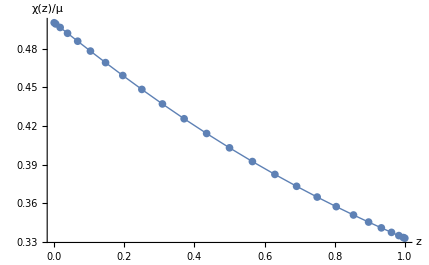

```mathematica
Show[p1,p2]
```

# Q-lattice 4D m2 = - 2, shooting

## analytics

## derive background eqs

### definitions

```mathematica
Unprotect[Laplacian];
```

```mathematica
<<EDCRGTCcode.m;
xIN={z,t,x,y};
g=1/z^2 DiagonalMatrix[{1/U[z], - U[z], V1[z],V2[z]}];
RGtensors[g,xIN];
```

gdd = (1/(z^2 U[z]) | 0 | 0 | 0
0 | -U[z]/z^2 | 0 | 0
0 | 0 | V1[z]/z^2 | 0
0 | 0 | 0 | V2[z]/z^2)

LineElement = d[z]^2/(z^2 U[z])-(d[t]^2 U[z])/z^2+(d[x]^2 V1[z])/z^2+(d[y]^2 V2[z])/z^2

gUU = (z^2 U[z] | 0 | 0 | 0
0 | -z^2/U[z] | 0 | 0
0 | 0 | z^2/V1[z] | 0
0 | 0 | 0 | z^2/V2[z])

gUU computed in 0.000874 sec

Gamma computed in 0.003864 sec

Riemann(dddd) computed in 0.008632 sec

Riemann(Uddd) computed in 0.0064 sec

Ricci computed in 0.013035 sec

Weyl computed in 0.022942 sec

Einstein computed in 0.00624 sec

All tasks completed in 0.09276 seconds

gauge field

```mathematica
Ad={0,At[z],0,0};
AU=Raise[Ad,1];

A2 = multiDot[AU, Ad,{1,1}];

Fdd=-covD[Ad]+ Transpose[covD[Ad]];
FUU= Raise[Fdd,1,2];
FdU=Raise[Fdd,2];
FUd=Raise[Fdd,1];
F2= multiDot[Fdd,FUU,{1,1},{2,2}];
```

complex scalar ϕ = e^(iT) χ

```mathematica
T = k x; X= χ[z];

dθd = covD[T]; 
dχd = covD[X];  

Dθ2 = multiDot[ Raise[dθd , 1] , dθd , {1,1} ];
Dχ2 = multiDot[ Raise[dχd , 1] , dχd , {1,1} ];
```

stress tensor

```mathematica
tχdd = Outer[Times,covD[X],covD[X]] - 1/2 gdd multiDot[Raise[covD[X],1], covD[X],{1,1}] - m2/2 gdd X^2;tθdd = X^2 Outer[Times,covD[T],covD[T]] - 1/2 X^2 gdd multiDot[Raise[covD[T],1], covD[T],{1,1}];
tlattdd = ( tχdd + tθdd  );
```

einstein eq

```mathematica
Einsdd=Rdd - 1/2 R gdd - 3gdd  - tlattdd- 1/2(multiDot[Fdd,FdU,{2,2}] - 1/4 F2 gdd ) ;

EinsUd=Raise[Einsdd,1];
```

neutral KG

```mathematica
KGχ = covDiv[Raise[covD[X],1],{1}] - X Dθ2 -m2 X ;
KGθ = X covDiv[Raise[covD[T],1],{1}]  + 2 multiDot[  dχd , Raise[dθd , 1] , {1,1}];
```

maxwell eq

```mathematica
EU = covDiv[FUU,{2,{1}}];
```

### find consistent set of eoms

```mathematica
e1aux =Simplify[ KGχ]
```

-((k^2 z^2+m2 V1[z]) χ[z])/V1[z]+1/2 z (2 z U'[z] χ'[z]+U[z] ((-4+(z V1'[z])/V1[z]+(z V2'[z])/V2[z]) χ'[z]+2 z χ''[z]))

```mathematica
e2aux = Simplify[ EU[[2]]  ]
```

-(z^4 (V1[z] At'[z] V2'[z]+V2[z] (At'[z] V1'[z]+2 V1[z] At''[z])))/(2 V1[z] V2[z])

```mathematica
e3aux = Simplify[  Einsdd[[1,1]] ]
```

1/(4 z^2 U[z] V1[z] V2[z])(z (V2[z] (2 k^2 z χ[z]^2+(-4 U[z]+z U'[z]) V1'[z])+z U[z] V1'[z] V2'[z])+V1[z] (z (-4 U[z]+z U'[z]) V2'[z]+V2[z] (-12+2 m2 χ[z]^2+z^4 At'[z]^2-4 z U'[z]-2 U[z] (-6+z^2 χ'[z]^2))))

```mathematica
e4aux = Simplify[ Einsdd[[2,2]] ]
```

-1/(4 z^2 V1[z]^2 V2[z]^2)U[z] (-z^2 U[z] V2[z]^2 V1'[z]^2+z V1[z] V2[z] (z U[z] V1'[z] V2'[z]+V2[z] (2 k^2 z χ[z]^2-4 U[z] V1'[z]+z U'[z] V1'[z]+2 z U[z] V1''[z]))+V1[z]^2 (-z^2 U[z] V2'[z]^2+V2[z]^2 (-12+2 m2 χ[z]^2+z^4 At'[z]^2-4 z U'[z]+2 U[z] (6+z^2 χ'[z]^2))+z V2[z] (z U'[z] V2'[z]+U[z] (-4 V2'[z]+2 z V2''[z]))))

```mathematica
e5aux = Simplify[ Einsdd[[3,3]] ]
```

1/(4 z^2 V2[z]^2)(-2 k^2 z^2 V2[z]^2 χ[z]^2+V1[z] (-z^2 U[z] V2'[z]^2+V2[z]^2 (-12+2 m2 χ[z]^2-z^4 At'[z]^2-8 z U'[z]+2 U[z] (6+z^2 χ'[z]^2)+2 z^2 U''[z])+2 z V2[z] (z U'[z] V2'[z]+U[z] (-2 V2'[z]+z V2''[z]))))

```mathematica
e6aux  = Simplify[ Einsdd[[4,4]] ]
```

1/(4 z^2 V1[z]^2)V2[z] (-z^2 U[z] V1'[z]^2+V1[z]^2 (-12+2 m2 χ[z]^2-z^4 At'[z]^2-8 z U'[z]+2 U[z] (6+z^2 χ'[z]^2)+2 z^2 U''[z])+2 z V1[z] (k^2 z χ[z]^2-2 U[z] V1'[z]+z U'[z] V1'[z]+z U[z] V1''[z]))

```mathematica
coeff1 = {a1->(2 U[z]^2 χ'[z])/(z (-2 U[z]+z U'[z])),a6->(U[z]^2 (-2 V2[z]+z V2'[z]))/(V2[z]^2 (2 U[z]-z U'[z])),a5->(U[z]^2 (-2 V1[z]+z V1'[z]))/(V1[z]^2 (2 U[z]-z U'[z])),a2->(U[z]^2 At'[z])/(z (-2 U[z]+z U'[z])), b3->(2 z U[z]^3)/(-2 U[z]+z U'[z]), a3->(U[z]^2 (-3 z V1[z] V2[z] U'[z]-U[z] (z V2[z] V1'[z]+V1[z] (-2 V2[z]+z V2'[z]))))/(V1[z] V2[z] (2 U[z]-z U'[z]))};
```

```mathematica
Collect[ e4aux + a5 e5aux + a6 e6aux  + a3 e3aux + b3 D[ e3aux,z] + a1 e1aux + a2 e2aux /. coeff1, {V1''[r],V2''[r], At''[r], χ''[r], U''[r]} /. r-> z , Simplify]
```

0

### simplify eoms

```mathematica
vars = {χ''[r], V1''[r],V2''[r],U''[r], At''[r],χ'[r],χ[r], U'[r],U[r], V1'[r], V1[r], V2'[r], V2[r],At'[r]} /. r-> z;
```

```mathematica
Collect[ 1/U[z] e1aux , vars, Simplify]
```

((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z]

```mathematica
Collect[- e2aux, vars, Simplify]
```

(z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z]

```mathematica
Collect[  e3aux , vars, Simplify]
```

3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2

```mathematica
Collect[  γ4 e4aux+ γ5 e5aux + γ6 e6aux  /. {γ4->-V2[z]/U[z]^2,γ5->V2[z]/(U[z] V1[z]),γ6->-1/U[z]} , vars, Simplify ]
```

(3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z]

```mathematica
Collect[  γ4 e4aux+ γ5 e5aux + γ6 e6aux /. {γ4->-V1[z]/U[z]^2,γ5->-1/U[z],γ6->V1[z]/(U[z] V2[z])}    , vars, Simplify ]
```

(3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z]

### all eqs

```mathematica
RepFields1= {U-> Function[z, (1-z) u[z]], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];

AllEqs = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. m2-> - 2;
```

### temperature

```mathematica
VU = {0,1,0,0};
Vd = Lower[VU,1];

DVdd = covD[Vd];
DVUU = Raise[DVdd,1,2];

κ2 = - 1/2 multiDot[DVdd, DVUU, {1,1},{2,2}];
```

```mathematica
FullSimplify[(√κ2)/(2 π) /. RepFields1  /. z-> 1 ]
```

(√(u[1]^2))/(4 π)

## IR asympt

```mathematica
χχSir[z_]= Sum[ χir[i] (1-z)^i, {i,0,5} ];
aSir[z_]= Sum[ air[i] (1-z)^i, {i,0,5} ];
uSir[z_]= Sum[ uir[i] (1-z)^i, {i,0,4} ];
V1Sir[z_]= Sum[ V1ir[i] (1-z)^i, {i,0,5} ];
V2Sir[z_]= Sum[ V2ir[i] (1-z)^i, {i,0,5} ];
```

```mathematica
IRasympt = {χχ-> χχSir, a-> aSir, u-> uSir,V1-> V1Sir, V2-> V2Sir};
```

#### IR coeff

```mathematica
IRcoeff = {χir[0]-> χH, air[0]-> aH , uir[0]-> uH, V1ir[0]-> V1H , V2ir[0]-> V2H , χir[1]->((k^2+(-2+uH) V1H) χH)/(uH V1H),air[1]->(aH (2 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2))))/(4 uH V1H),V1ir[1]->-(4 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2)))/(2 uH),V2ir[1]->-(V2H (aH^2+4 (-3+uH-χH^2)))/(2 uH) , χir[2]->(χH (4 k^2 V1H (-4+2 uH-χH^2)+k^4 (1+2 χH^2)+V1H^2 (aH^2+4 (4-4 uH+uH^2+χH^2))))/(4 uH^2 V1H^2),air[2]->(aH (8 k^4 χH^2 (1+2 χH^2)-4 k^2 V1H χH^2 (44-3 aH^2-12 uH+12 χH^2)+V1H^2 (3 aH^4+24 aH^2 (-3+uH-χH^2)+16 (27+3 uH^2+20 χH^2+3 χH^4-6 uH (3+χH^2)))))/(48 uH^2 V1H^2),V1ir[2]->(16 k^4 χH^2 (-1+χH^2)-4 k^2 V1H χH^2 (12-3 aH^2-8 uH+8 χH^2)+V1H^2 (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2))))/(16 uH^2 V1H),V2ir[2]->(V2H (-4 (-4+aH^2) k^2 χH^2+V1H (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2)))))/(16 uH^2 V1H),uir[1]->(aH^2 V1H-2 uH V1H+k^2 χH^2)/(2 V1H) , χir[3]->1/(72 uH^3 V1H^3)χH (k^6 (2+30 χH^2+24 χH^4)+2 k^4 V1H (27 uH (1+2 χH^2)-2 (27+80 χH^2+18 χH^4))+2 k^2 V1H^2 (aH^2 (17+5 χH^2)+4 (108+27 uH^2+77 χH^2+9 χH^4-27 uH (4+χH^2)))-V1H^3 (aH^4+aH^2 (116-54 uH+32 χH^2)-8 (-54 uH^2+9 uH^3+27 uH (4+χH^2)-2 (37+27 χH^2+3 χH^4)))),air[3]->1/(192 uH^3 V1H^3)aH (8 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (84+212 χH^2+48 χH^4-24 uH (1+2 χH^2)-aH^2 (4+11 χH^2))+2 k^2 V1H^2 χH^2 (9 aH^4+4 aH^2 (-61+18 uH-18 χH^2)+48 (39+3 uH^2+23 χH^2+3 χH^4-2 uH (11+3 χH^2)))+V1H^3 (3 aH^6+36 aH^4 (-3+uH-χH^2)+48 aH^2 (27+3 uH^2+19 χH^2+3 χH^4-6 uH (3+χH^2))+64 (-81+3 uH^3-97 χH^2-32 χH^4-3 χH^6-9 uH^2 (3+χH^2)+uH (81+60 χH^2+9 χH^4)))),V1ir[3]->-1/(144 uH^3 V1H^2)χH^2 (k^6 (48-96 χH^2)-48 V1H^3 (3 aH^2-4 (2+χH^2))+4 k^4 V1H (3 aH^2 (-5+2 χH^2)+4 (-12+29 χH^2+χH^4))+k^2 V1H^2 (9 aH^4+8 aH^2 (31+2 χH^2)-16 (15+38 χH^2+χH^4))),V2ir[3]->(V2H χH^2 (48 V1H^2 (3 aH^2-4 (2+χH^2))+k^2 V1H (9 aH^4+8 aH^2 (1+2 χH^2)-16 (15+2 χH^2+χH^4))-4 k^4 (aH^2 (3+6 χH^2)-4 (6+5 χH^2+χH^4))))/(144 uH^3 V1H^2),uir[2]->(8 k^4 χH^2 (1+2 χH^2)-8 k^2 V1H χH^2 (-3 aH^2+4 (3+χH^2))+V1H^2 (9 aH^4-40 aH^2 (3+χH^2)+16 (9+4 χH^2+χH^4)))/(48 uH V1H^2), χir[4]->1/(576 uH^4 V1H^4)χH (k^8 (1+96 χH^2+300 χH^4+144 χH^6)+16 k^6 V1H (-8-160 χH^2-190 χH^4-35 χH^6+uH (4+60 χH^2+48 χH^4))+V1H^4 (aH^4 (145-32 uH+42 χH^2)+16 aH^2 (248+54 uH^2+167 χH^2+21 χH^4-8 uH (29+8 χH^2))+16 (640-288 uH^3+36 uH^4+882 χH^2+255 χH^4+18 χH^6+216 uH^2 (4+χH^2)-32 uH (37+27 χH^2+3 χH^4)))-2 k^2 V1H^3 (aH^4 (7+3 χH^2)+4 aH^2 (286+214 χH^2+27 χH^4-8 uH (17+5 χH^2))-16 (-583+72 uH^3-803 χH^2-237 χH^4-18 χH^6-108 uH^2 (4+χH^2)+8 uH (108+77 χH^2+9 χH^4)))+2 k^4 V1H^2 (aH^2 (49+164 χH^2+38 χH^4)+8 (216+949 χH^2+463 χH^4+53 χH^6+54 uH^2 (1+2 χH^2)-8 uH (27+80 χH^2+18 χH^4)))),air[4]->1/(11520 uH^4 V1H^4)aH (16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-8 k^2 V1H^3 χH^2 (-45 aH^6+aH^4 (1772-540 uH+540 χH^2)-8 aH^2 (3035+270 uH^2+1886 χH^2+270 χH^4-30 uH (61+18 χH^2))-32 (-4021+90 uH^3-3815 χH^2-1068 χH^4-90 χH^6-90 uH^2 (11+3 χH^2)+90 uH (39+23 χH^2+3 χH^4)))-16 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+4 (97+806 χH^2+937 χH^4+179 χH^6-30 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (45 aH^4 (2+7 χH^2)+8 aH^2 (-385-1302 χH^2-328 χH^4+30 uH (4+11 χH^2))+16 (2106+6629 χH^2+3070 χH^4+359 χH^6+180 uH^2 (1+2 χH^2)-60 uH (21+53 χH^2+12 χH^4)))+V1H^4 (45 aH^8+720 aH^6 (-3+uH-χH^2)+80 aH^4 (486+54 uH^2+337 χH^2+54 χH^4-108 uH (3+χH^2))+128 aH^2 (-2430+90 uH^3-2674 χH^2-889 χH^4-90 χH^6-270 uH^2 (3+χH^2)+90 uH (27+19 χH^2+3 χH^4))+256 (3645+45 uH^4+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8-180 uH^3 (3+χH^2)+90 uH^2 (27+20 χH^2+3 χH^4)-60 uH (81+97 χH^2+32 χH^4+3 χH^6)))),V1ir[4]->1/(576 uH^4 V1H^3)χH^2 (8 k^8 (-5+18 χH^2+12 χH^4)-4 k^6 V1H (-172+48 uH+572 χH^2-96 uH χH^2+96 χH^4-12 χH^6+3 aH^2 (-7+3 χH^2+2 χH^4))-4 V1H^4 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))-k^4 V1H^2 (3 aH^4 (8+χH^2)-4 aH^2 (-347+140 χH^2+44 χH^4+uH (60-24 χH^2))+32 (18-192 χH^2-28 χH^4+χH^6+2 uH (-12+29 χH^2+χH^4)))+k^2 V1H^3 (aH^4 (330-36 uH+71 χH^2)+8 aH^2 (372+35 χH^2+χH^4-4 uH (31+2 χH^2))+16 (-250-373 χH^2-62 χH^4-χH^6+4 uH (15+38 χH^2+χH^4)))),V2ir[4]->1/(576 uH^4 V1H^3)V2H χH^2 (-4 k^6 (3 aH^2 (1+7 χH^2+6 χH^4)-4 (7+27 χH^2+18 χH^4+3 χH^6))-4 V1H^3 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))+k^2 V1H^2 (aH^4 (-202+36 uH-71 χH^2)+8 aH^2 (88+5 χH^2-χH^4+uH (4+8 χH^2))+16 (18+29 χH^2+14 χH^4+χH^6-4 uH (15+2 χH^2+χH^4)))+k^4 V1H (3 aH^4 (4+11 χH^2)+aH^2 (60+464 χH^2+112 χH^4-48 uH (1+2 χH^2))+32 (-36-59 χH^2-22 χH^4-2 χH^6+2 uH (6+5 χH^2+χH^4)))),uir[3]->1/(96 uH^2 V1H^3)(4 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (24-4 uH+76 χH^2-8 uH χH^2+18 χH^4-aH^2 (4+11 χH^2))+k^2 V1H^2 χH^2 (27 aH^4+4 aH^2 (-109+12 uH-32 χH^2)+16 (51+35 χH^2+5 χH^4-4 uH (3+χH^2)))+2 V1H^3 (3 aH^6+aH^4 (9 uH-25 (3+χH^2))+8 aH^2 (63+45 χH^2+7 χH^4-5 uH (3+χH^2))+16 (-27-25 χH^2-9 χH^4-χH^6+uH (9+4 χH^2+χH^4)))), χir[5]->1/(14400 uH^5 V1H^5)χH (k^10 (1+650 χH^2+5560 χH^4+8520 χH^6+2880 χH^8)+k^8 V1H (125 uH (1+96 χH^2+300 χH^4+144 χH^6)-2 (125+15656 χH^2+60084 χH^4+44076 χH^6+6880 χH^8))+2 k^6 V1H^2 (aH^2 (177+3864 χH^2+4868 χH^4+924 χH^6)+8 (1000+26557 χH^2+43832 χH^4+16572 χH^6+1675 χH^8+250 uH^2 (1+15 χH^2+12 χH^4)-125 uH (8+160 χH^2+190 χH^4+35 χH^6)))+k^2 V1H^4 (aH^4 (7933+6756 χH^2+980 χH^4-250 uH (7+3 χH^2))+16 (75500+4500 uH^4+167102 χH^2+89439 χH^4+16028 χH^6+900 χH^8-9000 uH^3 (4+χH^2)+1000 uH^2 (108+77 χH^2+9 χH^4)-250 uH (583+803 χH^2+237 χH^4+18 χH^6))+8 aH^2 (500 uH^2 (17+5 χH^2)-125 uH (286+214 χH^2+27 χH^4)+2 (18750+25009 χH^2+7678 χH^4+610 χH^6)))-k^4 V1H^3 (aH^4 (122+514 χH^2+137 χH^4)-16 (-18122-113764 χH^2-91633 χH^4-22778 χH^6-1715 χH^8+2250 uH^3 (1+2 χH^2)-500 uH^2 (27+80 χH^2+18 χH^4)+125 uH (216+949 χH^2+463 χH^4+53 χH^6))+aH^2 (-250 uH (49+164 χH^2+38 χH^4)+4 (6369+29792 χH^2+15006 χH^4+1764 χH^6)))-V1H^5 (aH^6 (236+70 χH^2)+aH^4 (30138+2000 uH^2+19892 χH^2+2680 χH^4-125 uH (145+42 χH^2))-16 aH^2 (2250 uH^3-500 uH^2 (29+8 χH^2)+125 uH (248+167 χH^2+21 χH^4)-2 (11118+13098 χH^2+3871 χH^4+305 χH^6))-16 (-9000 uH^4+900 uH^5+9000 uH^3 (4+χH^2)-2000 uH^2 (37+27 χH^2+3 χH^4)+125 uH (640+882 χH^2+255 χH^4+18 χH^6)-2 (18400+38626 χH^2+20215 χH^4+3474 χH^6+180 χH^8)))),air[5]->1/(138240 uH^5 V1H^5)aH (16 k^10 χH^2 (7+460 χH^2+2736 χH^4+3912 χH^6+1440 χH^8)-32 k^8 V1H χH^2 (455+11444 χH^2+34864 χH^4+25988 χH^6+4268 χH^8-30 uH (5+108 χH^2+276 χH^4+144 χH^6)-3 aH^2 (5+133 χH^2+421 χH^4+274 χH^6))+2 k^2 V1H^4 χH^2 (675 aH^8+12 aH^6 (-2899+900 uH-900 χH^2)+8 aH^4 (86195+8100 uH^2+54534 χH^2+8100 χH^4-120 uH (443+135 χH^2))+960 aH^2 (-6595+180 uH^3-6426 χH^2-1931 χH^4-180 χH^6-30 uH^2 (61+18 χH^2)+uH (6070+3772 χH^2+540 χH^4))+128 (202082+1350 uH^4+271868 χH^2+121749 χH^4+21870 χH^6+1350 χH^8-1800 uH^3 (11+3 χH^2)+2700 uH^2 (39+23 χH^2+3 χH^4)-60 uH (4021+3815 χH^2+1068 χH^4+90 χH^6)))+8 k^6 V1H^2 χH^2 (135 aH^4 (1+11 χH^2+15 χH^4)+4 aH^2 (-1331-14127 χH^2-20632 χH^4-4436 χH^6+450 uH (1+9 χH^2+10 χH^4))+16 (4535+44481 χH^2+66817 χH^4+25183 χH^6+2660 χH^8+450 uH^2 (1+7 χH^2+6 χH^4)-30 uH (97+806 χH^2+937 χH^4+179 χH^6)))-8 k^4 V1H^3 χH^2 (-45 aH^6 (4+17 χH^2)+aH^4 (8464+35266 χH^2+9405 χH^4-1350 uH (2+7 χH^2))-8 aH^2 (18009+73750 χH^2+37743 χH^4+4887 χH^6+450 uH^2 (4+11 χH^2)-30 uH (385+1302 χH^2+328 χH^4))-16 (-68056-262630 χH^2-187813 χH^4-45866 χH^6-3573 χH^8+1800 uH^3 (1+2 χH^2)-900 uH^2 (21+53 χH^2+12 χH^4)+30 uH (2106+6629 χH^2+3070 χH^4+359 χH^6)))+V1H^5 (135 aH^10+2700 aH^8 (-3+uH-χH^2)+288 aH^6 (675+75 uH^2+464 χH^2+75 χH^4-150 uH (3+χH^2))+32 aH^4 (-72900+2700 uH^3-78379 χH^2-26082 χH^4-2700 χH^6-8100 uH^2 (3+χH^2)+150 uH (486+337 χH^2+54 χH^4))+256 aH^2 (54675+675 uH^4+82946 χH^2+43118 χH^4+9162 χH^6+675 χH^8-2700 uH^3 (3+χH^2)+1350 uH^2 (27+19 χH^2+3 χH^4)-30 uH (2430+2674 χH^2+889 χH^4+90 χH^6))+512 (-65610+270 uH^5-144430 χH^2-109122 χH^4-35793 χH^6-5184 χH^8-270 χH^10-1350 uH^4 (3+χH^2)+900 uH^3 (27+20 χH^2+3 χH^4)-900 uH^2 (81+97 χH^2+32 χH^4+3 χH^6)+30 uH (3645+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8)))),V1ir[5]->1/(28800 uH^5 V1H^4)χH^2 (40 k^10 (-7+50 χH^2+144 χH^4+48 χH^6)+40 V1H^5 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))-4 k^8 V1H (15 aH^2 (-15-4 χH^2+32 χH^4+8 χH^6)-2 (1425-8094 χH^2-7744 χH^4-732 χH^6+48 χH^8+100 uH (-5+18 χH^2+12 χH^4)))-4 k^4 V1H^3 (aH^4 (-4397-892 χH^2+116 χH^4+75 uH (8+χH^2))+4 aH^2 (-17164+7174 χH^2+5828 χH^4+689 χH^6+150 uH^2 (-5+2 χH^2)-25 uH (-347+140 χH^2+44 χH^4))+16 (1648+13793 χH^2+4929 χH^4-67 χH^6-61 χH^8+50 uH^2 (-12+29 χH^2+χH^4)+50 uH (18-192 χH^2-28 χH^4+χH^6)))+k^2 V1H^4 (-5 aH^6 (236+55 χH^2)-4 aH^4 (25204+450 uH^2+10729 χH^2+1255 χH^4-25 uH (330+71 χH^2))-16 aH^2 (21280+3929 χH^2-968 χH^4-95 χH^6+100 uH^2 (31+2 χH^2)-50 uH (372+35 χH^2+χH^4))+64 (7890+11737 χH^2+4371 χH^4+309 χH^6-5 χH^8+50 uH^2 (15+38 χH^2+χH^4)-25 uH (250+373 χH^2+62 χH^4+χH^6)))-2 k^6 V1H^2 (225 aH^4 (1+χH^2)-16 (-2485+14877 χH^2+6193 χH^4-239 χH^6-124 χH^8+300 uH^2 (-1+2 χH^2)+50 uH (43-143 χH^2-24 χH^4+3 χH^6))+8 aH^2 (75 uH (-7+3 χH^2+2 χH^4)-2 (-1127+658 χH^2+704 χH^4+69 χH^6)))),V2ir[5]->1/(28800 uH^5 V1H^4)V2H χH^2 (-4 k^8 (5 aH^2 (5+108 χH^2+276 χH^4+144 χH^6)-2 (125+1734 χH^2+3184 χH^4+1612 χH^6+232 χH^8))+40 V1H^4 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))+k^2 V1H^3 (5 aH^6 (144+55 χH^2)+4 aH^4 (9454+450 uH^2+7589 χH^2+1255 χH^4-25 uH (202+71 χH^2))+16 aH^2 (-10620-7071 χH^2-1268 χH^4-95 χH^6+100 uH^2 (1+2 χH^2)-50 uH (-88-5 χH^2+χH^4))-64 (-1990-383 χH^2+61 χH^4+9 χH^6-5 χH^8+50 uH^2 (15+2 χH^2+χH^4)-25 uH (18+29 χH^2+14 χH^4+χH^6)))+4 k^4 V1H^2 (aH^4 (-1277-5112 χH^2-1334 χH^4+75 uH (4+11 χH^2))-4 aH^2 (-1346+2726 χH^2+1952 χH^4+231 χH^6+150 uH^2 (1+2 χH^2)-25 uH (15+116 χH^2+28 χH^4))+16 (1728+5593 χH^2+3319 χH^4+613 χH^6+29 χH^8+50 uH^2 (6+5 χH^2+χH^4)-50 uH (36+59 χH^2+22 χH^4+2 χH^6)))+2 k^6 V1H (75 aH^4 (1+9 χH^2+10 χH^4)-8 aH^2 (-109-1644 χH^2-2352 χH^4-442 χH^6+75 uH (1+7 χH^2+6 χH^4))+16 (-865-4987 χH^2-5013 χH^4-1491 χH^6-126 χH^8+50 uH (7+27 χH^2+18 χH^4+3 χH^6)))),uir[4]->1/(11520 uH^3 V1H^4)(16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-16 k^2 V1H^3 χH^2 (-90 aH^6+aH^4 (2521-405 uH+765 χH^2)-4 aH^2 (5158+90 uH^2+3184 χH^2+450 χH^4-15 uH (109+32 χH^2))+16 (1591+1641 χH^2+501 χH^4+45 χH^6+30 uH^2 (3+χH^2)-15 uH (51+35 χH^2+5 χH^4)))-32 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+2 (60+584 χH^2+736 χH^4+143 χH^6-15 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (135 aH^4 (2+7 χH^2)+8 aH^2 (-709-2406 χH^2-601 χH^4+30 uH (4+11 χH^2))+16 (918+3787 χH^2+1876 χH^4+227 χH^6+30 uH^2 (1+2 χH^2)-30 uH (12+38 χH^2+9 χH^4)))+3 V1H^4 (75 aH^8+40 aH^6 (12 uH-23 (3+χH^2))-128 aH^2 (1215+1371 χH^2+454 χH^4+45 χH^6+25 uH^2 (3+χH^2)-10 uH (63+45 χH^2+7 χH^4))+16 aH^4 (45 uH^2-250 uH (3+χH^2)+3 (720+501 χH^2+80 χH^4))+256 (405+580 χH^2+302 χH^4+67 χH^6+5 χH^8+5 uH^2 (9+4 χH^2+χH^4)-10 uH (27+25 χH^2+9 χH^4+χH^6))))};
```

```mathematica
eqtempIR = Collect[ Series[ {x AllEqs[[1]] , AllEqs[[2]] ,x  AllEqs[[3]], x  AllEqs[[4]], x  AllEqs[[5]]   } /. IRasympt /. z-> 1 - x , {x,0,4}] /. IRcoeff  , x, Simplify ]
```

{0,0,0,0,0}

```mathematica
Solve[eqtempIR ==0 , { χir[5], air[5], V1ir[5],V2ir[5], uir[4]  } ][[1]] // Simplify
```

## UV asympt

```mathematica
χχSuv[z_]= Sum[ χuv[i] z^i, {i,0,8} ];
aSuv[z_]= Sum[ auv[i] z^i, {i,0,8} ];
uSuv[z_]= Sum[ uuv[i] z^i, {i,0,8} ];
V1Suv[z_]= Sum[ V1uv[i] z^i, {i,0,8} ];
V2Suv[z_]= Sum[ V2uv[i] z^i, {i,0,8} ];
```

```mathematica
UVasympt = {χχ-> χχSuv, a-> aSuv, u-> uSuv,V1-> V1Suv, V2-> V2Suv};
```

#### UV coeff

```mathematica
UVcoeff = {uuv[0]->1,V2uv[0]->1,V1uv[0]->1,χuv[0]->λ,χuv[1]->Oλ,uuv[1]->1,V1uv[1]->0,V2uv[1]->0,auv[1]->-ρ,auv[0]->μ,uuv[2]->1-λ^2/2,V1uv[2]->-λ^2/2,V2uv[2]->-λ^2/2,auv[2]->-ρ,χuv[2]->1/2 λ (k^2+λ^2),auv[3]->1/6 (-6 ρ-λ^2 (μ+ρ)),χuv[3]->1/12 (2 k^2 Oλ-λ (-2-10 Oλ λ+λ^2+2 uuv[3])), V2uv[3]->-(4 Oλ λ)/3-V1uv[3] , χuv[4]->1/24 (12 Oλ^2 λ+λ (k^4+10 k^2 λ^2+8 λ^4-(μ+ρ)^2)-4 Oλ (-2+λ^2+2 uuv[3])),auv[4]->1/6 (-6 ρ-Oλ λ (μ+ρ)-λ^2 (μ+ρ)),uuv[4]->1/12 (-4 Oλ^2-2 λ^4+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[4]->1/6 (-2 Oλ^2-λ^2 (3 k^2+λ^2)),V2uv[4]->1/6 (-2 Oλ^2-λ^4), χuv[5]->1/120 (k^4 Oλ+28 Oλ^3+Oλ (104 λ^4-9 (μ+ρ)^2)-18 λ^3 (-2+λ^2+2 uuv[3])-2 k^2 λ (-14-31 Oλ λ+7 λ^2+14 uuv[3]+3 V1uv[3])),auv[5]->1/60 (-60 ρ-4 Oλ^2 (μ+ρ)-10 Oλ λ (μ+ρ)-(10+3 k^2) λ^2 (μ+ρ)-5 λ^4 (μ+ρ)),uuv[5]->1/12 (-4 Oλ^2-λ^4-2 Oλ λ (k^2+2 λ^2)+2 λ^2 (-1+uuv[3])+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[5]->1/30 λ (-17 k^2 Oλ+λ (-2-10 Oλ λ+λ^2+2 uuv[3]+3 V1uv[3])),V2uv[5]->1/30 λ (-5 k^2 Oλ+λ (-2-14 Oλ λ+λ^2+2 uuv[3]-3 V1uv[3])), χuv[6]->1/720 (k^6 λ+95 k^4 λ^3+k^2 (284 Oλ^2 λ+λ (302 λ^4-37 (μ+ρ)^2)-12 Oλ (-6+3 λ^2+6 uuv[3]+2 V1uv[3]))+λ (756 Oλ^2 λ^2+16 λ^4+192 λ^6-λ^2 (64+55 μ^2+110 μ ρ+55 ρ^2-64 uuv[3])+4 (16-32 uuv[3]+16 uuv[3]^2+9 V1uv[3]^2)+4 Oλ λ (-59 λ^2+2 (59-59 uuv[3]+6 V1uv[3])))),auv[6]->1/180 (-180 ρ-12 Oλ^2 (μ+ρ)-14 λ^4 (μ+ρ)-Oλ λ (30+11 k^2+32 λ^2) (μ+ρ)-λ^2 (μ+ρ) (32+9 k^2-2 uuv[3])),uuv[6]->1/60 (-(5+6 k^2) λ^4-6 λ^6-2 Oλ^2 (10+k^2+12 λ^2)+λ^2 (-2 k^4+5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3]))-2 Oλ λ (6+5 k^2+7 λ^2-6 uuv[3]+6 V1uv[3])+3 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[6]->1/360 (-52 k^4 λ^2-144 Oλ^2 λ^2-36 λ^6-2 k^2 (26 Oλ^2+53 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-24 Oλ λ (-2+λ^2+2 uuv[3]-2 V1uv[3])+180 V1uv[3]-90 λ^2 V1uv[3]-180 uuv[3] V1uv[3]+126 V1uv[3]^2),V2uv[6]->1/360 (-12 k^4 λ^2+16 Oλ^2 λ^2-36 λ^6-12 k^2 (Oλ^2+3 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-180 V1uv[3]+90 λ^2 V1uv[3]+180 uuv[3] V1uv[3]+126 V1uv[3]^2+96 Oλ λ (-2+λ^2+2 uuv[3]+3 V1uv[3])), χuv[7]->1/10080(Oλ^3 (952 k^2+8200 λ^2)-4 Oλ^2 λ (-1114+557 λ^2+1114 uuv[3]-264 V1uv[3])-λ (9 (212 λ^4-25 (μ+ρ)^2) (-2+λ^2+2 uuv[3])+3 k^4 (-102+51 λ^2+102 uuv[3]+44 V1uv[3])+2 k^2 λ^2 (-2018+1009 λ^2+2018 uuv[3]+420 V1uv[3]))+2 Oλ (k^6+1071 k^4 λ^2+250 λ^4+4776 λ^6+k^2 (4854 λ^4-109 (μ+ρ)^2)-λ^2 (827 μ^2+1654 μ ρ+827 ρ^2-1000 (-1+uuv[3]))+4 (250-500 uuv[3]+250 uuv[3]^2+99 V1uv[3]^2))),auv[7]->1/2520(-7 (28+23 k^2) λ^4 (μ+ρ)-141 λ^6 (μ+ρ)-8 Oλ^2 (21+4 k^2+53 λ^2) (μ+ρ)+λ^2 (μ+ρ) (-448-126 k^2-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3])-2 Oλ λ (μ+ρ) (77 k^2+206 λ^2+6 (41-6 uuv[3]+6 V1uv[3]))-18 (3 μ V1uv[3]^2+ρ (140+3 V1uv[3]^2))),uuv[7]->1/360 (-64 Oλ^3 λ-17 λ^6-4 Oλ^2 (40+3 k^2+31 λ^2-10 uuv[3])+λ^4 (-68-24 k^2+38 uuv[3])-4 Oλ λ (2 k^4+21 λ^2+28 λ^4+k^2 (15+19 λ^2)-2 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3]))-6 λ^2 (2 k^4-5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3])+k^2 (4-4 uuv[3]-3 V1uv[3]))+18 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[7]->1/2520(-448 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (74 k^4+397 k^2 λ^2+196 λ^4+19 (μ+ρ)^2)+272 λ^4 uuv[3]+3 k^2 λ^2 (-226+113 λ^2+226 uuv[3]-228 V1uv[3])+40 Oλ^2 (-10+5 λ^2+10 uuv[3]-3 V1uv[3])-6 λ^4 V1uv[3]-270 μ^2 V1uv[3]-540 μ ρ V1uv[3]-270 ρ^2 V1uv[3]),V2uv[7]->1/2520(-288 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (14 k^4+223 k^2 λ^2+194 λ^4-71 (μ+ρ)^2)+272 λ^4 uuv[3]+6 λ^4 V1uv[3]+270 μ^2 V1uv[3]+540 μ ρ V1uv[3]+270 ρ^2 V1uv[3]+40 Oλ^2 (-10+5 λ^2+10 uuv[3]+3 V1uv[3])-3 k^2 λ^2 (-34+17 λ^2+34 uuv[3]+48 V1uv[3])), χuv[8]->1/40320(k^8 λ+12912 Oλ^4 λ+1444 k^6 λ^3+16 Oλ^2 λ (4198 λ^4-277 (μ+ρ)^2)-5344 Oλ^3 (-2+λ^2+2 uuv[3])-16 Oλ (1391 λ^6-117 λ^2 (μ+ρ)^2-234 (μ+ρ)^2 (-1+uuv[3])+λ^4 (-2782+2782 uuv[3]-342 V1uv[3]))+2 k^4 (2308 Oλ^2 λ+λ (4912 λ^4-131 (μ+ρ)^2)-72 Oλ (-2+λ^2+2 uuv[3]+V1uv[3]))+λ (2430 λ^6+9388 λ^8+225 (μ+ρ)^4-20 λ^4 (486+203 μ^2+406 μ ρ+203 ρ^2-486 uuv[3])+216 λ^2 (45-90 uuv[3]+45 uuv[3]^2+19 V1uv[3]^2))+4 k^2 λ (12048 Oλ^2 λ^2+382 λ^4+4516 λ^6-λ^2 (1528+989 μ^2+1978 μ ρ+989 ρ^2-1528 uuv[3]-222 V1uv[3])-2 Oλ λ (-2738+1369 λ^2+2738 uuv[3]+234 V1uv[3])+4 (382+382 uuv[3]^2-111 V1uv[3]+153 V1uv[3]^2+uuv[3] (-764+111 V1uv[3])))),auv[8]->1/5040(-372 Oλ^3 λ (μ+ρ)-227 λ^6 (μ+ρ)-2 λ^4 (μ+ρ) (251+143 k^2-55 uuv[3])-2 Oλ^2 (μ+ρ) (218+32 k^2+399 λ^2-50 uuv[3])+2 λ^2 (μ+ρ) (-448-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3]+9 k^2 (4 uuv[3]+3 (-6+V1uv[3])))-108 μ V1uv[3]^2-2 Oλ λ (μ+ρ) (492+22 k^4+412 λ^2+451 λ^4+k^2 (154+323 λ^2)-13 μ^2-26 μ ρ-13 ρ^2-72 uuv[3]+72 V1uv[3])-36 ρ (140+3 V1uv[3]^2)),uuv[8]->1/5040(-304 Oλ^4-896 Oλ^3 λ-5 (51+112 k^2) λ^6-358 λ^8-4 Oλ^2 (560+4 k^4+434 λ^2+641 λ^4+6 k^2 (7+43 λ^2)-51 μ^2-102 μ ρ-51 ρ^2-140 uuv[3])+λ^4 (-884-336 k^2-272 k^4+265 μ^2+530 μ ρ+265 ρ^2+464 uuv[3])+252 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)-2 Oλ λ (56 k^4+434 λ^4+k^2 (706+389 λ^2-286 uuv[3]-84 V1uv[3])-56 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3])+λ^2 (1288-700 uuv[3]+384 V1uv[3]))+2 λ^2 (-454-84 k^4-8 k^6+210 μ^2+420 μ ρ+210 ρ^2+488 uuv[3]-34 uuv[3]^2-288 V1uv[3]^2+k^2 (71 μ^2+142 μ ρ+71 ρ^2+42 (-4+4 uuv[3]+3 V1uv[3])))),V1uv[8]->1/5040(-304 Oλ^4-100 k^6 λ^2-4 k^4 (25 Oλ^2+124 λ^4)+Oλ^2 (-2564 λ^4+162 (μ+ρ)^2)+k^2 λ (-2348 Oλ^2 λ+λ (-1036 λ^4+289 (μ+ρ)^2)+2 Oλ (-958+479 λ^2+958 uuv[3]-588 V1uv[3]))+2 Oλ λ^3 (-322+161 λ^2+322 uuv[3]-6 V1uv[3])+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]-840 V1uv[3])-4 (38+38 uuv[3]^2-420 V1uv[3]-297 V1uv[3]^2+uuv[3] (-76+420 V1uv[3])))),V2uv[8]->1/5040(-304 Oλ^4-16 k^6 λ^2-16 k^4 (Oλ^2+17 λ^4)+Oλ^2 (-436 λ^4+162 (μ+ρ)^2)-k^2 λ (1256 Oλ^2 λ+λ (560 λ^4+47 (μ+ρ)^2)-202 Oλ (-2+λ^2+2 uuv[3]))+2 Oλ λ^3 (721 λ^2+2 (-721+721 uuv[3]+795 V1uv[3]))+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]+840 V1uv[3])-4 (38+38 uuv[3]^2+420 V1uv[3]-297 V1uv[3]^2-4 uuv[3] (19+105 V1uv[3]))))};
```

```mathematica
eqtempUV = Collect[ Series[ {z^-2 AllEqs[[1]],z^-3 AllEqs[[2]],z AllEqs[[3]] ,z  AllEqs[[4]],z AllEqs[[5]]  } /. UVasympt  , {z,0,7}] /. UVcoeff  , z, Simplify ]
```

{0,0,0,0,0}

```mathematica
Solve[eqtempUV ==0 , {χuv[b], auv[b],uuv[b],V1uv[b], V2uv[b] } ][[1]] // Simplify
```

## UV asympt v2

### all eqs

```mathematica
RepFields1= {U-> Function[z, (1-z) u[z]], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];

AllEqs = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. m2-> - 2;
```

```mathematica
χχSuv[z_]= Sum[ χuv[i] z^i, {i,0,8} ];
aSuv[z_]= Sum[ auv[i] z^i, {i,0,8} ];
uSuv[z_]= Sum[ uuv[i] z^i, {i,0,8} ];
V1Suv[z_]= Sum[ V1uv[i] z^i, {i,0,8} ];
V2Suv[z_]= Sum[ V2uv[i] z^i, {i,0,8} ];
```

```mathematica
UVasympt = {χχ-> χχSuv, a-> aSuv, u-> uSuv,V1-> V1Suv, V2-> V2Suv};
```

#### UV coeff

```mathematica
UVcoeff = {uuv[0]->1,V2uv[0]->1,V1uv[0]->1,χuv[0]->λ,χuv[1]->Oλ,auv[0]-> μ,auv[1]-> - ρ, V1uv[1]->-1+uuv[1],V2uv[1]->-1+uuv[1] , χuv[2]->1/4 (λ (2 k^2+2 λ^2-(-1+uuv[1])^2)-4 Oλ (-1+uuv[1])),auv[2]->1/2 (ρ (-3+uuv[1])+μ (-1+uuv[1])),uuv[2]->1/4 (-2 λ^2+(1+uuv[1])^2),V1uv[2]->1/4 (-2 λ^2+(-1+uuv[1])^2),V2uv[2]->1/4 (-2 λ^2+(-1+uuv[1])^2) };
```

```mathematica
eqtempUV = Collect[ Series[ {z^-2 AllEqs[[1]],z^-3 AllEqs[[2]],z AllEqs[[3]] ,z  AllEqs[[4]],z AllEqs[[5]]  } /. UVasympt  , {z,0,1}] /. UVcoeff  , z, Simplify ]
```

{0,0,0,0,0}

```mathematica
b=2;
```

```mathematica
Solve[eqtempUV ==0 , {χuv[b], auv[b],uuv[b],V1uv[b], V2uv[b] } ][[1]] // Simplify
```

{χuv[2]→1/4 (λ (2 k^2+2 λ^2-(-1+uuv[1])^2)-4 Oλ (-1+uuv[1])),auv[2]→1/2 (ρ (-3+uuv[1])+μ (-1+uuv[1])),uuv[2]→1/4 (-2 λ^2+(1+uuv[1])^2),V1uv[2]→1/4 (-2 λ^2+(-1+uuv[1])^2),V2uv[2]→1/4 (-2 λ^2+(-1+uuv[1])^2)}

```mathematica
Collect[ Series[ uSuv[z] /. UVcoeff  /. uuv[1]-> 1 + c0 , {z,0,2}], z, FullSimplify]
```

1+(1+c0) z+1/4 z^2 ((2+c0)^2-2 λ^2)

```mathematica
Series[ V1Suv[z] /. UVcoeff /. uuv[1]->  1 + c0  , {z,0,2}]
```

1+c0 z+1/4 (c0^2-2 λ^2) z^2+O[z]^3

```mathematica
Series[ V2Suv[z] /. UVcoeff /. uuv[1]->  1 + c0  , {z,0,2}]
```

1+c0 z+1/4 (c0^2-2 λ^2) z^2+O[z]^3

```mathematica
ds2 = 1/z^2(  - (1 - z) u[z] dt^2 + dz^2/((1- z) u[z]) + V1[z] dx^2 + V2[z] dy^2 );
```

```mathematica
repz = {z-> zp(1 + b/zp) , dz-> a dzp};
```

```mathematica
Series[ Coefficient[ ds2 /. UVasympt /. UVcoeff , dx^2], {z,0,0}]
```

1/z^2+(-1+uuv[1])/z+1/4 (1-2 λ^2-2 uuv[1]+uuv[1]^2)+O[z]^1

```mathematica
Series[ Coefficient[ ds2 /. UVasympt /. UVcoeff/. repz  , dx^2], {zp,0,0}]
```

(1/4+1/b^2-1/b-λ^2/2-uuv[1]/2+uuv[1]/b+uuv[1]^2/4+b V1uv[3]+b^2 V1uv[4]+b^3 V1uv[5]+b^4 V1uv[6]+b^5 V1uv[7]+b^6 V1uv[8])+O[zp]^1

## numerics v1, FindRoot

## preliminaries

### message catch

```mathematica
NDSolve::ndsz="Something went horribly wrong";

Unprotect[Message];
Message[mm :NDSolve::ndsz,m___]:=Block[{$inMsg=True,result},
Message[mm,m];

Abort[]]/;!TrueQ[$inMsg]
Protect[Message];
```

### eoms

```mathematica
RepFields1= {U-> Function[z, (1-z) u[z]], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];
```

```mathematica
AllEqs[μ_,k1_] = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. m2-> - 2 /. {k-> k1 μ};
```

### IR asymptotics

#### IR coeff

```mathematica
IRcoeff = {χir[0]-> χH, air[0]-> aH , uir[0]-> uH, V1ir[0]-> V1H , V2ir[0]-> V2H , χir[1]->((k^2+(-2+uH) V1H) χH)/(uH V1H),air[1]->(aH (2 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2))))/(4 uH V1H),V1ir[1]->-(4 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2)))/(2 uH),V2ir[1]->-(V2H (aH^2+4 (-3+uH-χH^2)))/(2 uH) , χir[2]->(χH (4 k^2 V1H (-4+2 uH-χH^2)+k^4 (1+2 χH^2)+V1H^2 (aH^2+4 (4-4 uH+uH^2+χH^2))))/(4 uH^2 V1H^2),air[2]->(aH (8 k^4 χH^2 (1+2 χH^2)-4 k^2 V1H χH^2 (44-3 aH^2-12 uH+12 χH^2)+V1H^2 (3 aH^4+24 aH^2 (-3+uH-χH^2)+16 (27+3 uH^2+20 χH^2+3 χH^4-6 uH (3+χH^2)))))/(48 uH^2 V1H^2),V1ir[2]->(16 k^4 χH^2 (-1+χH^2)-4 k^2 V1H χH^2 (12-3 aH^2-8 uH+8 χH^2)+V1H^2 (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2))))/(16 uH^2 V1H),V2ir[2]->(V2H (-4 (-4+aH^2) k^2 χH^2+V1H (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2)))))/(16 uH^2 V1H),uir[1]->(aH^2 V1H-2 uH V1H+k^2 χH^2)/(2 V1H) , χir[3]->1/(72 uH^3 V1H^3)χH (k^6 (2+30 χH^2+24 χH^4)+2 k^4 V1H (27 uH (1+2 χH^2)-2 (27+80 χH^2+18 χH^4))+2 k^2 V1H^2 (aH^2 (17+5 χH^2)+4 (108+27 uH^2+77 χH^2+9 χH^4-27 uH (4+χH^2)))-V1H^3 (aH^4+aH^2 (116-54 uH+32 χH^2)-8 (-54 uH^2+9 uH^3+27 uH (4+χH^2)-2 (37+27 χH^2+3 χH^4)))),air[3]->1/(192 uH^3 V1H^3)aH (8 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (84+212 χH^2+48 χH^4-24 uH (1+2 χH^2)-aH^2 (4+11 χH^2))+2 k^2 V1H^2 χH^2 (9 aH^4+4 aH^2 (-61+18 uH-18 χH^2)+48 (39+3 uH^2+23 χH^2+3 χH^4-2 uH (11+3 χH^2)))+V1H^3 (3 aH^6+36 aH^4 (-3+uH-χH^2)+48 aH^2 (27+3 uH^2+19 χH^2+3 χH^4-6 uH (3+χH^2))+64 (-81+3 uH^3-97 χH^2-32 χH^4-3 χH^6-9 uH^2 (3+χH^2)+uH (81+60 χH^2+9 χH^4)))),V1ir[3]->-1/(144 uH^3 V1H^2)χH^2 (k^6 (48-96 χH^2)-48 V1H^3 (3 aH^2-4 (2+χH^2))+4 k^4 V1H (3 aH^2 (-5+2 χH^2)+4 (-12+29 χH^2+χH^4))+k^2 V1H^2 (9 aH^4+8 aH^2 (31+2 χH^2)-16 (15+38 χH^2+χH^4))),V2ir[3]->(V2H χH^2 (48 V1H^2 (3 aH^2-4 (2+χH^2))+k^2 V1H (9 aH^4+8 aH^2 (1+2 χH^2)-16 (15+2 χH^2+χH^4))-4 k^4 (aH^2 (3+6 χH^2)-4 (6+5 χH^2+χH^4))))/(144 uH^3 V1H^2),uir[2]->(8 k^4 χH^2 (1+2 χH^2)-8 k^2 V1H χH^2 (-3 aH^2+4 (3+χH^2))+V1H^2 (9 aH^4-40 aH^2 (3+χH^2)+16 (9+4 χH^2+χH^4)))/(48 uH V1H^2), χir[4]->1/(576 uH^4 V1H^4)χH (k^8 (1+96 χH^2+300 χH^4+144 χH^6)+16 k^6 V1H (-8-160 χH^2-190 χH^4-35 χH^6+uH (4+60 χH^2+48 χH^4))+V1H^4 (aH^4 (145-32 uH+42 χH^2)+16 aH^2 (248+54 uH^2+167 χH^2+21 χH^4-8 uH (29+8 χH^2))+16 (640-288 uH^3+36 uH^4+882 χH^2+255 χH^4+18 χH^6+216 uH^2 (4+χH^2)-32 uH (37+27 χH^2+3 χH^4)))-2 k^2 V1H^3 (aH^4 (7+3 χH^2)+4 aH^2 (286+214 χH^2+27 χH^4-8 uH (17+5 χH^2))-16 (-583+72 uH^3-803 χH^2-237 χH^4-18 χH^6-108 uH^2 (4+χH^2)+8 uH (108+77 χH^2+9 χH^4)))+2 k^4 V1H^2 (aH^2 (49+164 χH^2+38 χH^4)+8 (216+949 χH^2+463 χH^4+53 χH^6+54 uH^2 (1+2 χH^2)-8 uH (27+80 χH^2+18 χH^4)))),air[4]->1/(11520 uH^4 V1H^4)aH (16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-8 k^2 V1H^3 χH^2 (-45 aH^6+aH^4 (1772-540 uH+540 χH^2)-8 aH^2 (3035+270 uH^2+1886 χH^2+270 χH^4-30 uH (61+18 χH^2))-32 (-4021+90 uH^3-3815 χH^2-1068 χH^4-90 χH^6-90 uH^2 (11+3 χH^2)+90 uH (39+23 χH^2+3 χH^4)))-16 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+4 (97+806 χH^2+937 χH^4+179 χH^6-30 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (45 aH^4 (2+7 χH^2)+8 aH^2 (-385-1302 χH^2-328 χH^4+30 uH (4+11 χH^2))+16 (2106+6629 χH^2+3070 χH^4+359 χH^6+180 uH^2 (1+2 χH^2)-60 uH (21+53 χH^2+12 χH^4)))+V1H^4 (45 aH^8+720 aH^6 (-3+uH-χH^2)+80 aH^4 (486+54 uH^2+337 χH^2+54 χH^4-108 uH (3+χH^2))+128 aH^2 (-2430+90 uH^3-2674 χH^2-889 χH^4-90 χH^6-270 uH^2 (3+χH^2)+90 uH (27+19 χH^2+3 χH^4))+256 (3645+45 uH^4+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8-180 uH^3 (3+χH^2)+90 uH^2 (27+20 χH^2+3 χH^4)-60 uH (81+97 χH^2+32 χH^4+3 χH^6)))),V1ir[4]->1/(576 uH^4 V1H^3)χH^2 (8 k^8 (-5+18 χH^2+12 χH^4)-4 k^6 V1H (-172+48 uH+572 χH^2-96 uH χH^2+96 χH^4-12 χH^6+3 aH^2 (-7+3 χH^2+2 χH^4))-4 V1H^4 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))-k^4 V1H^2 (3 aH^4 (8+χH^2)-4 aH^2 (-347+140 χH^2+44 χH^4+uH (60-24 χH^2))+32 (18-192 χH^2-28 χH^4+χH^6+2 uH (-12+29 χH^2+χH^4)))+k^2 V1H^3 (aH^4 (330-36 uH+71 χH^2)+8 aH^2 (372+35 χH^2+χH^4-4 uH (31+2 χH^2))+16 (-250-373 χH^2-62 χH^4-χH^6+4 uH (15+38 χH^2+χH^4)))),V2ir[4]->1/(576 uH^4 V1H^3)V2H χH^2 (-4 k^6 (3 aH^2 (1+7 χH^2+6 χH^4)-4 (7+27 χH^2+18 χH^4+3 χH^6))-4 V1H^3 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))+k^2 V1H^2 (aH^4 (-202+36 uH-71 χH^2)+8 aH^2 (88+5 χH^2-χH^4+uH (4+8 χH^2))+16 (18+29 χH^2+14 χH^4+χH^6-4 uH (15+2 χH^2+χH^4)))+k^4 V1H (3 aH^4 (4+11 χH^2)+aH^2 (60+464 χH^2+112 χH^4-48 uH (1+2 χH^2))+32 (-36-59 χH^2-22 χH^4-2 χH^6+2 uH (6+5 χH^2+χH^4)))),uir[3]->1/(96 uH^2 V1H^3)(4 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (24-4 uH+76 χH^2-8 uH χH^2+18 χH^4-aH^2 (4+11 χH^2))+k^2 V1H^2 χH^2 (27 aH^4+4 aH^2 (-109+12 uH-32 χH^2)+16 (51+35 χH^2+5 χH^4-4 uH (3+χH^2)))+2 V1H^3 (3 aH^6+aH^4 (9 uH-25 (3+χH^2))+8 aH^2 (63+45 χH^2+7 χH^4-5 uH (3+χH^2))+16 (-27-25 χH^2-9 χH^4-χH^6+uH (9+4 χH^2+χH^4)))), χir[5]->1/(14400 uH^5 V1H^5)χH (k^10 (1+650 χH^2+5560 χH^4+8520 χH^6+2880 χH^8)+k^8 V1H (125 uH (1+96 χH^2+300 χH^4+144 χH^6)-2 (125+15656 χH^2+60084 χH^4+44076 χH^6+6880 χH^8))+2 k^6 V1H^2 (aH^2 (177+3864 χH^2+4868 χH^4+924 χH^6)+8 (1000+26557 χH^2+43832 χH^4+16572 χH^6+1675 χH^8+250 uH^2 (1+15 χH^2+12 χH^4)-125 uH (8+160 χH^2+190 χH^4+35 χH^6)))+k^2 V1H^4 (aH^4 (7933+6756 χH^2+980 χH^4-250 uH (7+3 χH^2))+16 (75500+4500 uH^4+167102 χH^2+89439 χH^4+16028 χH^6+900 χH^8-9000 uH^3 (4+χH^2)+1000 uH^2 (108+77 χH^2+9 χH^4)-250 uH (583+803 χH^2+237 χH^4+18 χH^6))+8 aH^2 (500 uH^2 (17+5 χH^2)-125 uH (286+214 χH^2+27 χH^4)+2 (18750+25009 χH^2+7678 χH^4+610 χH^6)))-k^4 V1H^3 (aH^4 (122+514 χH^2+137 χH^4)-16 (-18122-113764 χH^2-91633 χH^4-22778 χH^6-1715 χH^8+2250 uH^3 (1+2 χH^2)-500 uH^2 (27+80 χH^2+18 χH^4)+125 uH (216+949 χH^2+463 χH^4+53 χH^6))+aH^2 (-250 uH (49+164 χH^2+38 χH^4)+4 (6369+29792 χH^2+15006 χH^4+1764 χH^6)))-V1H^5 (aH^6 (236+70 χH^2)+aH^4 (30138+2000 uH^2+19892 χH^2+2680 χH^4-125 uH (145+42 χH^2))-16 aH^2 (2250 uH^3-500 uH^2 (29+8 χH^2)+125 uH (248+167 χH^2+21 χH^4)-2 (11118+13098 χH^2+3871 χH^4+305 χH^6))-16 (-9000 uH^4+900 uH^5+9000 uH^3 (4+χH^2)-2000 uH^2 (37+27 χH^2+3 χH^4)+125 uH (640+882 χH^2+255 χH^4+18 χH^6)-2 (18400+38626 χH^2+20215 χH^4+3474 χH^6+180 χH^8)))),air[5]->1/(138240 uH^5 V1H^5)aH (16 k^10 χH^2 (7+460 χH^2+2736 χH^4+3912 χH^6+1440 χH^8)-32 k^8 V1H χH^2 (455+11444 χH^2+34864 χH^4+25988 χH^6+4268 χH^8-30 uH (5+108 χH^2+276 χH^4+144 χH^6)-3 aH^2 (5+133 χH^2+421 χH^4+274 χH^6))+2 k^2 V1H^4 χH^2 (675 aH^8+12 aH^6 (-2899+900 uH-900 χH^2)+8 aH^4 (86195+8100 uH^2+54534 χH^2+8100 χH^4-120 uH (443+135 χH^2))+960 aH^2 (-6595+180 uH^3-6426 χH^2-1931 χH^4-180 χH^6-30 uH^2 (61+18 χH^2)+uH (6070+3772 χH^2+540 χH^4))+128 (202082+1350 uH^4+271868 χH^2+121749 χH^4+21870 χH^6+1350 χH^8-1800 uH^3 (11+3 χH^2)+2700 uH^2 (39+23 χH^2+3 χH^4)-60 uH (4021+3815 χH^2+1068 χH^4+90 χH^6)))+8 k^6 V1H^2 χH^2 (135 aH^4 (1+11 χH^2+15 χH^4)+4 aH^2 (-1331-14127 χH^2-20632 χH^4-4436 χH^6+450 uH (1+9 χH^2+10 χH^4))+16 (4535+44481 χH^2+66817 χH^4+25183 χH^6+2660 χH^8+450 uH^2 (1+7 χH^2+6 χH^4)-30 uH (97+806 χH^2+937 χH^4+179 χH^6)))-8 k^4 V1H^3 χH^2 (-45 aH^6 (4+17 χH^2)+aH^4 (8464+35266 χH^2+9405 χH^4-1350 uH (2+7 χH^2))-8 aH^2 (18009+73750 χH^2+37743 χH^4+4887 χH^6+450 uH^2 (4+11 χH^2)-30 uH (385+1302 χH^2+328 χH^4))-16 (-68056-262630 χH^2-187813 χH^4-45866 χH^6-3573 χH^8+1800 uH^3 (1+2 χH^2)-900 uH^2 (21+53 χH^2+12 χH^4)+30 uH (2106+6629 χH^2+3070 χH^4+359 χH^6)))+V1H^5 (135 aH^10+2700 aH^8 (-3+uH-χH^2)+288 aH^6 (675+75 uH^2+464 χH^2+75 χH^4-150 uH (3+χH^2))+32 aH^4 (-72900+2700 uH^3-78379 χH^2-26082 χH^4-2700 χH^6-8100 uH^2 (3+χH^2)+150 uH (486+337 χH^2+54 χH^4))+256 aH^2 (54675+675 uH^4+82946 χH^2+43118 χH^4+9162 χH^6+675 χH^8-2700 uH^3 (3+χH^2)+1350 uH^2 (27+19 χH^2+3 χH^4)-30 uH (2430+2674 χH^2+889 χH^4+90 χH^6))+512 (-65610+270 uH^5-144430 χH^2-109122 χH^4-35793 χH^6-5184 χH^8-270 χH^10-1350 uH^4 (3+χH^2)+900 uH^3 (27+20 χH^2+3 χH^4)-900 uH^2 (81+97 χH^2+32 χH^4+3 χH^6)+30 uH (3645+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8)))),V1ir[5]->1/(28800 uH^5 V1H^4)χH^2 (40 k^10 (-7+50 χH^2+144 χH^4+48 χH^6)+40 V1H^5 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))-4 k^8 V1H (15 aH^2 (-15-4 χH^2+32 χH^4+8 χH^6)-2 (1425-8094 χH^2-7744 χH^4-732 χH^6+48 χH^8+100 uH (-5+18 χH^2+12 χH^4)))-4 k^4 V1H^3 (aH^4 (-4397-892 χH^2+116 χH^4+75 uH (8+χH^2))+4 aH^2 (-17164+7174 χH^2+5828 χH^4+689 χH^6+150 uH^2 (-5+2 χH^2)-25 uH (-347+140 χH^2+44 χH^4))+16 (1648+13793 χH^2+4929 χH^4-67 χH^6-61 χH^8+50 uH^2 (-12+29 χH^2+χH^4)+50 uH (18-192 χH^2-28 χH^4+χH^6)))+k^2 V1H^4 (-5 aH^6 (236+55 χH^2)-4 aH^4 (25204+450 uH^2+10729 χH^2+1255 χH^4-25 uH (330+71 χH^2))-16 aH^2 (21280+3929 χH^2-968 χH^4-95 χH^6+100 uH^2 (31+2 χH^2)-50 uH (372+35 χH^2+χH^4))+64 (7890+11737 χH^2+4371 χH^4+309 χH^6-5 χH^8+50 uH^2 (15+38 χH^2+χH^4)-25 uH (250+373 χH^2+62 χH^4+χH^6)))-2 k^6 V1H^2 (225 aH^4 (1+χH^2)-16 (-2485+14877 χH^2+6193 χH^4-239 χH^6-124 χH^8+300 uH^2 (-1+2 χH^2)+50 uH (43-143 χH^2-24 χH^4+3 χH^6))+8 aH^2 (75 uH (-7+3 χH^2+2 χH^4)-2 (-1127+658 χH^2+704 χH^4+69 χH^6)))),V2ir[5]->1/(28800 uH^5 V1H^4)V2H χH^2 (-4 k^8 (5 aH^2 (5+108 χH^2+276 χH^4+144 χH^6)-2 (125+1734 χH^2+3184 χH^4+1612 χH^6+232 χH^8))+40 V1H^4 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))+k^2 V1H^3 (5 aH^6 (144+55 χH^2)+4 aH^4 (9454+450 uH^2+7589 χH^2+1255 χH^4-25 uH (202+71 χH^2))+16 aH^2 (-10620-7071 χH^2-1268 χH^4-95 χH^6+100 uH^2 (1+2 χH^2)-50 uH (-88-5 χH^2+χH^4))-64 (-1990-383 χH^2+61 χH^4+9 χH^6-5 χH^8+50 uH^2 (15+2 χH^2+χH^4)-25 uH (18+29 χH^2+14 χH^4+χH^6)))+4 k^4 V1H^2 (aH^4 (-1277-5112 χH^2-1334 χH^4+75 uH (4+11 χH^2))-4 aH^2 (-1346+2726 χH^2+1952 χH^4+231 χH^6+150 uH^2 (1+2 χH^2)-25 uH (15+116 χH^2+28 χH^4))+16 (1728+5593 χH^2+3319 χH^4+613 χH^6+29 χH^8+50 uH^2 (6+5 χH^2+χH^4)-50 uH (36+59 χH^2+22 χH^4+2 χH^6)))+2 k^6 V1H (75 aH^4 (1+9 χH^2+10 χH^4)-8 aH^2 (-109-1644 χH^2-2352 χH^4-442 χH^6+75 uH (1+7 χH^2+6 χH^4))+16 (-865-4987 χH^2-5013 χH^4-1491 χH^6-126 χH^8+50 uH (7+27 χH^2+18 χH^4+3 χH^6)))),uir[4]->1/(11520 uH^3 V1H^4)(16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-16 k^2 V1H^3 χH^2 (-90 aH^6+aH^4 (2521-405 uH+765 χH^2)-4 aH^2 (5158+90 uH^2+3184 χH^2+450 χH^4-15 uH (109+32 χH^2))+16 (1591+1641 χH^2+501 χH^4+45 χH^6+30 uH^2 (3+χH^2)-15 uH (51+35 χH^2+5 χH^4)))-32 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+2 (60+584 χH^2+736 χH^4+143 χH^6-15 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (135 aH^4 (2+7 χH^2)+8 aH^2 (-709-2406 χH^2-601 χH^4+30 uH (4+11 χH^2))+16 (918+3787 χH^2+1876 χH^4+227 χH^6+30 uH^2 (1+2 χH^2)-30 uH (12+38 χH^2+9 χH^4)))+3 V1H^4 (75 aH^8+40 aH^6 (12 uH-23 (3+χH^2))-128 aH^2 (1215+1371 χH^2+454 χH^4+45 χH^6+25 uH^2 (3+χH^2)-10 uH (63+45 χH^2+7 χH^4))+16 aH^4 (45 uH^2-250 uH (3+χH^2)+3 (720+501 χH^2+80 χH^4))+256 (405+580 χH^2+302 χH^4+67 χH^6+5 χH^8+5 uH^2 (9+4 χH^2+χH^4)-10 uH (27+25 χH^2+9 χH^4+χH^6))))};
```

```mathematica
repIR = {k-> k1 μ};
```

```mathematica
χχSIR[χH_,aH_,uH_,V1H_,V2H_,μ_,k1_][z_]= Sum[ χir[i] (1-z)^i, {i,0,5} ] /. IRcoeff/. repIR;
aSIR[χH_,aH_,uH_,V1H_,V2H_,μ_,k1_][z_]= Sum[ air[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
uSIR[χH_,aH_,uH_,V1H_,V2H_,μ_,k1_][z_]= Sum[ uir[i] (1-z)^i, {i,0,4} ]/. IRcoeff/. repIR;
V1SIR[χH_,aH_,uH_,V1H_,V2H_,μ_,k1_][z_]= Sum[ V1ir[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
V2SIR[χH_,aH_,uH_,V1H_,V2H_,μ_,k1_][z_]= Sum[ V2ir[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
```

### UV asymptotics

#### UV coeff

```mathematica
UVcoeff = {uuv[0]->1,V2uv[0]->1,V1uv[0]->1,χuv[0]->λ,χuv[1]->Oλ,uuv[1]->1,V1uv[1]->0,V2uv[1]->0,auv[1]->-ρ,auv[0]->μ,uuv[2]->1-λ^2/2,V1uv[2]->-λ^2/2,V2uv[2]->-λ^2/2,auv[2]->-ρ,χuv[2]->1/2 λ (k^2+λ^2),auv[3]->1/6 (-6 ρ-λ^2 (μ+ρ)),χuv[3]->1/12 (2 k^2 Oλ-λ (-2-10 Oλ λ+λ^2+2 uuv[3])), V2uv[3]->-(4 Oλ λ)/3-V1uv[3] , χuv[4]->1/24 (12 Oλ^2 λ+λ (k^4+10 k^2 λ^2+8 λ^4-(μ+ρ)^2)-4 Oλ (-2+λ^2+2 uuv[3])),auv[4]->1/6 (-6 ρ-Oλ λ (μ+ρ)-λ^2 (μ+ρ)),uuv[4]->1/12 (-4 Oλ^2-2 λ^4+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[4]->1/6 (-2 Oλ^2-λ^2 (3 k^2+λ^2)),V2uv[4]->1/6 (-2 Oλ^2-λ^4), χuv[5]->1/120 (k^4 Oλ+28 Oλ^3+Oλ (104 λ^4-9 (μ+ρ)^2)-18 λ^3 (-2+λ^2+2 uuv[3])-2 k^2 λ (-14-31 Oλ λ+7 λ^2+14 uuv[3]+3 V1uv[3])),auv[5]->1/60 (-60 ρ-4 Oλ^2 (μ+ρ)-10 Oλ λ (μ+ρ)-(10+3 k^2) λ^2 (μ+ρ)-5 λ^4 (μ+ρ)),uuv[5]->1/12 (-4 Oλ^2-λ^4-2 Oλ λ (k^2+2 λ^2)+2 λ^2 (-1+uuv[3])+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[5]->1/30 λ (-17 k^2 Oλ+λ (-2-10 Oλ λ+λ^2+2 uuv[3]+3 V1uv[3])),V2uv[5]->1/30 λ (-5 k^2 Oλ+λ (-2-14 Oλ λ+λ^2+2 uuv[3]-3 V1uv[3])), χuv[6]->1/720 (k^6 λ+95 k^4 λ^3+k^2 (284 Oλ^2 λ+λ (302 λ^4-37 (μ+ρ)^2)-12 Oλ (-6+3 λ^2+6 uuv[3]+2 V1uv[3]))+λ (756 Oλ^2 λ^2+16 λ^4+192 λ^6-λ^2 (64+55 μ^2+110 μ ρ+55 ρ^2-64 uuv[3])+4 (16-32 uuv[3]+16 uuv[3]^2+9 V1uv[3]^2)+4 Oλ λ (-59 λ^2+2 (59-59 uuv[3]+6 V1uv[3])))),auv[6]->1/180 (-180 ρ-12 Oλ^2 (μ+ρ)-14 λ^4 (μ+ρ)-Oλ λ (30+11 k^2+32 λ^2) (μ+ρ)-λ^2 (μ+ρ) (32+9 k^2-2 uuv[3])),uuv[6]->1/60 (-(5+6 k^2) λ^4-6 λ^6-2 Oλ^2 (10+k^2+12 λ^2)+λ^2 (-2 k^4+5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3]))-2 Oλ λ (6+5 k^2+7 λ^2-6 uuv[3]+6 V1uv[3])+3 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[6]->1/360 (-52 k^4 λ^2-144 Oλ^2 λ^2-36 λ^6-2 k^2 (26 Oλ^2+53 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-24 Oλ λ (-2+λ^2+2 uuv[3]-2 V1uv[3])+180 V1uv[3]-90 λ^2 V1uv[3]-180 uuv[3] V1uv[3]+126 V1uv[3]^2),V2uv[6]->1/360 (-12 k^4 λ^2+16 Oλ^2 λ^2-36 λ^6-12 k^2 (Oλ^2+3 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-180 V1uv[3]+90 λ^2 V1uv[3]+180 uuv[3] V1uv[3]+126 V1uv[3]^2+96 Oλ λ (-2+λ^2+2 uuv[3]+3 V1uv[3])), χuv[7]->1/10080(Oλ^3 (952 k^2+8200 λ^2)-4 Oλ^2 λ (-1114+557 λ^2+1114 uuv[3]-264 V1uv[3])-λ (9 (212 λ^4-25 (μ+ρ)^2) (-2+λ^2+2 uuv[3])+3 k^4 (-102+51 λ^2+102 uuv[3]+44 V1uv[3])+2 k^2 λ^2 (-2018+1009 λ^2+2018 uuv[3]+420 V1uv[3]))+2 Oλ (k^6+1071 k^4 λ^2+250 λ^4+4776 λ^6+k^2 (4854 λ^4-109 (μ+ρ)^2)-λ^2 (827 μ^2+1654 μ ρ+827 ρ^2-1000 (-1+uuv[3]))+4 (250-500 uuv[3]+250 uuv[3]^2+99 V1uv[3]^2))),auv[7]->1/2520(-7 (28+23 k^2) λ^4 (μ+ρ)-141 λ^6 (μ+ρ)-8 Oλ^2 (21+4 k^2+53 λ^2) (μ+ρ)+λ^2 (μ+ρ) (-448-126 k^2-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3])-2 Oλ λ (μ+ρ) (77 k^2+206 λ^2+6 (41-6 uuv[3]+6 V1uv[3]))-18 (3 μ V1uv[3]^2+ρ (140+3 V1uv[3]^2))),uuv[7]->1/360 (-64 Oλ^3 λ-17 λ^6-4 Oλ^2 (40+3 k^2+31 λ^2-10 uuv[3])+λ^4 (-68-24 k^2+38 uuv[3])-4 Oλ λ (2 k^4+21 λ^2+28 λ^4+k^2 (15+19 λ^2)-2 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3]))-6 λ^2 (2 k^4-5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3])+k^2 (4-4 uuv[3]-3 V1uv[3]))+18 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[7]->1/2520(-448 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (74 k^4+397 k^2 λ^2+196 λ^4+19 (μ+ρ)^2)+272 λ^4 uuv[3]+3 k^2 λ^2 (-226+113 λ^2+226 uuv[3]-228 V1uv[3])+40 Oλ^2 (-10+5 λ^2+10 uuv[3]-3 V1uv[3])-6 λ^4 V1uv[3]-270 μ^2 V1uv[3]-540 μ ρ V1uv[3]-270 ρ^2 V1uv[3]),V2uv[7]->1/2520(-288 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (14 k^4+223 k^2 λ^2+194 λ^4-71 (μ+ρ)^2)+272 λ^4 uuv[3]+6 λ^4 V1uv[3]+270 μ^2 V1uv[3]+540 μ ρ V1uv[3]+270 ρ^2 V1uv[3]+40 Oλ^2 (-10+5 λ^2+10 uuv[3]+3 V1uv[3])-3 k^2 λ^2 (-34+17 λ^2+34 uuv[3]+48 V1uv[3])), χuv[8]->1/40320(k^8 λ+12912 Oλ^4 λ+1444 k^6 λ^3+16 Oλ^2 λ (4198 λ^4-277 (μ+ρ)^2)-5344 Oλ^3 (-2+λ^2+2 uuv[3])-16 Oλ (1391 λ^6-117 λ^2 (μ+ρ)^2-234 (μ+ρ)^2 (-1+uuv[3])+λ^4 (-2782+2782 uuv[3]-342 V1uv[3]))+2 k^4 (2308 Oλ^2 λ+λ (4912 λ^4-131 (μ+ρ)^2)-72 Oλ (-2+λ^2+2 uuv[3]+V1uv[3]))+λ (2430 λ^6+9388 λ^8+225 (μ+ρ)^4-20 λ^4 (486+203 μ^2+406 μ ρ+203 ρ^2-486 uuv[3])+216 λ^2 (45-90 uuv[3]+45 uuv[3]^2+19 V1uv[3]^2))+4 k^2 λ (12048 Oλ^2 λ^2+382 λ^4+4516 λ^6-λ^2 (1528+989 μ^2+1978 μ ρ+989 ρ^2-1528 uuv[3]-222 V1uv[3])-2 Oλ λ (-2738+1369 λ^2+2738 uuv[3]+234 V1uv[3])+4 (382+382 uuv[3]^2-111 V1uv[3]+153 V1uv[3]^2+uuv[3] (-764+111 V1uv[3])))),auv[8]->1/5040(-372 Oλ^3 λ (μ+ρ)-227 λ^6 (μ+ρ)-2 λ^4 (μ+ρ) (251+143 k^2-55 uuv[3])-2 Oλ^2 (μ+ρ) (218+32 k^2+399 λ^2-50 uuv[3])+2 λ^2 (μ+ρ) (-448-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3]+9 k^2 (4 uuv[3]+3 (-6+V1uv[3])))-108 μ V1uv[3]^2-2 Oλ λ (μ+ρ) (492+22 k^4+412 λ^2+451 λ^4+k^2 (154+323 λ^2)-13 μ^2-26 μ ρ-13 ρ^2-72 uuv[3]+72 V1uv[3])-36 ρ (140+3 V1uv[3]^2)),uuv[8]->1/5040(-304 Oλ^4-896 Oλ^3 λ-5 (51+112 k^2) λ^6-358 λ^8-4 Oλ^2 (560+4 k^4+434 λ^2+641 λ^4+6 k^2 (7+43 λ^2)-51 μ^2-102 μ ρ-51 ρ^2-140 uuv[3])+λ^4 (-884-336 k^2-272 k^4+265 μ^2+530 μ ρ+265 ρ^2+464 uuv[3])+252 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)-2 Oλ λ (56 k^4+434 λ^4+k^2 (706+389 λ^2-286 uuv[3]-84 V1uv[3])-56 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3])+λ^2 (1288-700 uuv[3]+384 V1uv[3]))+2 λ^2 (-454-84 k^4-8 k^6+210 μ^2+420 μ ρ+210 ρ^2+488 uuv[3]-34 uuv[3]^2-288 V1uv[3]^2+k^2 (71 μ^2+142 μ ρ+71 ρ^2+42 (-4+4 uuv[3]+3 V1uv[3])))),V1uv[8]->1/5040(-304 Oλ^4-100 k^6 λ^2-4 k^4 (25 Oλ^2+124 λ^4)+Oλ^2 (-2564 λ^4+162 (μ+ρ)^2)+k^2 λ (-2348 Oλ^2 λ+λ (-1036 λ^4+289 (μ+ρ)^2)+2 Oλ (-958+479 λ^2+958 uuv[3]-588 V1uv[3]))+2 Oλ λ^3 (-322+161 λ^2+322 uuv[3]-6 V1uv[3])+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]-840 V1uv[3])-4 (38+38 uuv[3]^2-420 V1uv[3]-297 V1uv[3]^2+uuv[3] (-76+420 V1uv[3])))),V2uv[8]->1/5040(-304 Oλ^4-16 k^6 λ^2-16 k^4 (Oλ^2+17 λ^4)+Oλ^2 (-436 λ^4+162 (μ+ρ)^2)-k^2 λ (1256 Oλ^2 λ+λ (560 λ^4+47 (μ+ρ)^2)-202 Oλ (-2+λ^2+2 uuv[3]))+2 Oλ λ^3 (721 λ^2+2 (-721+721 uuv[3]+795 V1uv[3]))+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]+840 V1uv[3])-4 (38+38 uuv[3]^2+420 V1uv[3]-297 V1uv[3]^2-4 uuv[3] (19+105 V1uv[3]))))};
```

```mathematica
repUV = {λ-> λ1 μ , k-> k1 μ, V1uv[3]-> Vv, uuv[3]-> m0};
```

```mathematica
χχSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ χuv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
aSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ auv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
uSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ uuv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
V1SUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ V1uv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
V2SUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ V2uv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
```

### integration from the horizon

```mathematica
(*intIR[ConstantArray[1, 12]][0.001,0.001,0.5]*)
```

```mathematica
intIR[backsoln_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsIR,systemIR,χH,aH,uH,V1H,V2H,μ,ρ,Oλ,m0,Vv,U1H,ϕH,λ1,k1},

(* assignments *)
{μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,uH,k1} = backsoln;

(* asymptotics *)
bcsIR= { 
χχ[1-ϵH] ==  χχSIR[χH,aH,uH,V1H,V2H,μ,k1][1-ϵH],
χχ'[1-ϵH] ==χχSIR[χH,aH,uH,V1H,V2H,μ,k1]'[1-ϵH],
a[1-ϵH] ==  aSIR[χH,aH,uH,V1H,V2H,μ,k1][1-ϵH],
a'[1-ϵH] ==aSIR[χH,aH,uH,V1H,V2H,μ,k1]'[1-ϵH],
u[1-ϵH] ==  uSIR[χH,aH,uH,V1H,V2H,μ,k1][1-ϵH],
V1[1-ϵH]==V1SIR[χH,aH,uH,V1H,V2H,μ,k1][1-ϵH],
V1'[1-ϵH]==V1SIR[χH,aH,uH,V1H,V2H,μ,k1]'[1-ϵH],
V2[1-ϵH]==V2SIR[χH,aH,uH,V1H,V2H,μ,k1][1-ϵH],
V2'[1-ϵH]==V2SIR[χH,aH,uH,V1H,V2H,μ,k1]'[1-ϵH]};

(* system to be integrated *)
systemIR={AllEqs[μ,k1][[1]]==0, AllEqs[μ,k1][[2]]==0, AllEqs[μ,k1][[3]]==0, AllEqs[μ,k1][[4]]==0, AllEqs[μ,k1][[5]]==0, bcsIR };

NDSolve[   systemIR, {χχ,a,u,V1,V2},{z,zmatch-0.001,1-ϵH}]

 ];
```

### integration from the boundary

```mathematica
(*intUV[ConstantArray[1, 12]][0.001,0.001,0.5]*)
```

```mathematica
intUV[backsoln_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsUV,systemUV,χH,aH,uH,V1H,V2H,μ,ρ,Oλ,m0,Vv,U1H,ϕH,λ1,k1},

(* assignments *)
{μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,uH,k1} = backsoln;

(* asymptotics *)
bcsUV= { 
χχ[ϵ] ==  χχSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
χχ'[ϵ] ==χχSUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
a[ϵ] ==  aSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
a'[ϵ] ==aSUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
u[ϵ] ==  uSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V1[ϵ] ==  V1SUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V1'[ϵ] ==V1SUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
V2[ϵ] ==  V2SUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V2'[ϵ] ==V2SUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ]
};

(* system to be integrated *)
systemUV={AllEqs[μ,k1][[1]]==0, AllEqs[μ,k1][[2]]==0, AllEqs[μ,k1][[3]]==0, AllEqs[μ,k1][[4]]==0, AllEqs[μ,k1][[5]]==0, bcsUV };

NDSolve[   systemUV, {χχ,a,u,V1,V2},{z,ϵ,zmatch+0.001}]

 ];
```

### find seed from RN

```mathematica
solnRN = {χχ-> Function[z, 0], V1-> Function[z, 1 ], V2-> Function[z, 1 ], a-> Function[z, μ ], u-> Function[z, 1+z+z^2-(z^3 μ^2)/4 ]};
```

```mathematica
Simplify[ AllEqs[μ, k] /. solnRN ]
```

{0,0,0,0,0}

```mathematica
QLatticeConst = {ρ-> 0,Oλ-> 0, m0-> - μ^2/4, Vv-> 0 ,uH->  3-μ^2/4, aH-> μ , V1H-> 1 , V2H-> 1, χH-> 0.1};
```

```mathematica
SeedQLattice[λ1_,μ_,k1_]= {μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,uH,k1}  /. QLatticeConst;
```

### matching eqs

```mathematica
MatchingEqs[μ_?NumberQ,ρ_?NumberQ,Oλ_?NumberQ,m0_?NumberQ,Vv_?NumberQ,χH_?NumberQ,aH_?NumberQ,V1H_?NumberQ,V2H_?NumberQ, λ1_?NumberQ,uH_?NumberQ,k1_?NumberQ]:= Module[{ϵ,ϵH,zmatch, intIRaux,intUVaux, backsoln},

ϵ=0.1;ϵH=0.001;zmatch = 0.5;

backsoln = { μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H, λ1,uH,k1};

intUVaux=intUV[backsoln][ϵ,ϵH,zmatch];
intIRaux=intIR[backsoln][ϵ,ϵH,zmatch];

(N[{χχ[zmatch], χχ'[zmatch],a[zmatch],a'[zmatch], u[zmatch], V1[zmatch],V1'[zmatch], V2[zmatch],V2'[zmatch]} /. intIRaux   ][[1]]  
-
N[{χχ[zmatch], χχ'[zmatch],a[zmatch],a'[zmatch], u[zmatch], V1[zmatch],V1'[zmatch], V2[zmatch],V2'[zmatch]}/. intUVaux ][[1]])

];

GetQLattice[backsoln_]:= Module[{ μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H, λ1,uH,k1, μSeed,ρSeed,OλSeed,m0Seed,VvSeed,χHSeed,aHSeed,V1HSeed,V2HSeed}, 

{μSeed,ρSeed,OλSeed,m0Seed,VvSeed,χHSeed,aHSeed,V1HSeed,V2HSeed, λ1,uH,k1}= backsoln;

{μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,uH,k1} /.  FindRoot[ MatchingEqs[μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,uH,k1], {{μ , μSeed}, {ρ,ρSeed}, {Oλ,OλSeed}, {m0,m0Seed }, {Vv,VvSeed}, {χH, χHSeed}, {aH, aHSeed}, {V1H, V1HSeed}, {V2H, V2HSeed}}] 


];
```

## run FindRoot

```mathematica
Soln1 = GetQLattice[  SeedQLattice[0.1,0.5,1] ];// AbsoluteTiming
```

{10.26,Null}

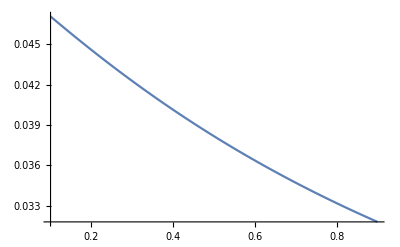

```mathematica
Plot[Evaluate[  χχ[z] /. intUV[Soln1][0.1,0.0001,0.9] ] , {z, 0.1, 0.9} ]
```

## numerics v2, Broyden

## preliminaries

### message catch

```mathematica
NDSolve::ndsz="Something went horribly wrong";

Unprotect[Message];
Message[mm :NDSolve::ndsz,m___]:=Block[{$inMsg=True,result},
Message[mm,m];

Abort[]]/;!TrueQ[$inMsg]
Protect[Message];
```

### eoms

```mathematica
RepFields1= {U-> Function[z, (1-z) u[z]], At-> Function[ z, (1-z) a[z] ], χ-> Function[z, z χχ[z] ] };
```

```mathematica
EQ1 = ((-m2-(k^2 z^2)/V1[z]) χ[z])/U[z]+(-2 z+(z^2 U'[z])/U[z]+(z^2 V1'[z])/(2 V1[z])+(z^2 V2'[z])/(2 V2[z])) χ'[z]+z^2 χ''[z];
EQ2 = (z^4 At'[z] V1'[z])/(2 V1[z])+(z^4 At'[z] V2'[z])/(2 V2[z])+z^4 At''[z];

EQ3 = 3/z^2+((m2/(2 z^2)+k^2/(2 V1[z])) χ[z]^2)/U[z]+(-3/z^2+1/4 z^2 At'[z]^2)/U[z]-V2'[z]/(z V2[z])+(V1'[z] (-1/z+V2'[z]/(4 V2[z])))/V1[z]+(U'[z] (-1/z+V1'[z]/(4 V1[z])+V2'[z]/(4 V2[z])))/U[z]-1/2 χ'[z]^2;
EQ4 = (3 V2[z])/z^2+(((m2 V2[z])/(2 z^2)-(k^2 V2[z])/(2 V1[z])) χ[z]^2)/U[z]+(V2[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]+(U'[z] (-V2[z]/z-(V2[z] V1'[z])/(4 V1[z])+(3 V2'[z])/4))/U[z]-(2 V2'[z])/z+(V1'[z] V2'[z])/(4 V1[z])-V2'[z]^2/(2 V2[z])+1/2 V2[z] χ'[z]^2+V2''[z];
EQ5 = (3 V1[z])/z^2+(((3 k^2)/2+(m2 V1[z])/(2 z^2)) χ[z]^2)/U[z]+(V1[z] (-3/z^2+1/4 z^2 At'[z]^2))/U[z]-V1'[z]^2/(2 V1[z])+V1'[z] (-2/z+V2'[z]/(4 V2[z]))+(U'[z] ((3 V1'[z])/4+V1[z] (-1/z-V2'[z]/(4 V2[z]))))/U[z]+1/2 V1[z] χ'[z]^2+V1''[z];
```

```mathematica
AllEqs[μ_,k1_] = {EQ1,EQ2,EQ3,EQ4,EQ5} /. RepFields1 /. m2-> - 2 /. {k-> k1 μ};
```

### IR asymptotics

#### IR coeff

```mathematica
IRcoeff = {χir[0]-> χH, air[0]-> aH , uir[0]-> uH, V1ir[0]-> V1H , V2ir[0]-> V2H , χir[1]->((k^2+(-2+uH) V1H) χH)/(uH V1H),air[1]->(aH (2 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2))))/(4 uH V1H),V1ir[1]->-(4 k^2 χH^2+V1H (aH^2+4 (-3+uH-χH^2)))/(2 uH),V2ir[1]->-(V2H (aH^2+4 (-3+uH-χH^2)))/(2 uH) , χir[2]->1/(4 uH^2 V1H^2)χH (4 k^2 V1H (-4+2 uH-χH^2)+k^4 (1+2 χH^2)+V1H^2 (aH^2+4 (4-4 uH+uH^2+χH^2))),air[2]->1/(48 uH^2 V1H^2)aH (8 k^4 χH^2 (1+2 χH^2)-4 k^2 V1H χH^2 (44-3 aH^2-12 uH+12 χH^2)+V1H^2 (3 aH^4+24 aH^2 (-3+uH-χH^2)+16 (27+3 uH^2+20 χH^2+3 χH^4-6 uH (3+χH^2)))),V1ir[2]->1/(16 uH^2 V1H)(16 k^4 χH^2 (-1+χH^2)-4 k^2 V1H χH^2 (12-3 aH^2-8 uH+8 χH^2)+V1H^2 (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2)))),V2ir[2]->1/(16 uH^2 V1H)V2H (-4 (-4+aH^2) k^2 χH^2+V1H (aH^4+8 aH^2 (-3+uH-χH^2)+16 (9+uH^2+4 χH^2+χH^4-2 uH (3+χH^2)))),uir[1]->(aH^2 V1H-2 uH V1H+k^2 χH^2)/(2 V1H) , χir[3]->1/(72 uH^3 V1H^3)χH (k^6 (2+30 χH^2+24 χH^4)+2 k^4 V1H (27 uH (1+2 χH^2)-2 (27+80 χH^2+18 χH^4))+2 k^2 V1H^2 (aH^2 (17+5 χH^2)+4 (108+27 uH^2+77 χH^2+9 χH^4-27 uH (4+χH^2)))-V1H^3 (aH^4+aH^2 (116-54 uH+32 χH^2)-8 (-54 uH^2+9 uH^3+27 uH (4+χH^2)-2 (37+27 χH^2+3 χH^4)))),air[3]->1/(192 uH^3 V1H^3)aH (8 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (84+212 χH^2+48 χH^4-24 uH (1+2 χH^2)-aH^2 (4+11 χH^2))+2 k^2 V1H^2 χH^2 (9 aH^4+4 aH^2 (-61+18 uH-18 χH^2)+48 (39+3 uH^2+23 χH^2+3 χH^4-2 uH (11+3 χH^2)))+V1H^3 (3 aH^6+36 aH^4 (-3+uH-χH^2)+48 aH^2 (27+3 uH^2+19 χH^2+3 χH^4-6 uH (3+χH^2))+64 (-81+3 uH^3-97 χH^2-32 χH^4-3 χH^6-9 uH^2 (3+χH^2)+uH (81+60 χH^2+9 χH^4)))),V1ir[3]->-1/(144 uH^3 V1H^2)χH^2 (k^6 (48-96 χH^2)-48 V1H^3 (3 aH^2-4 (2+χH^2))+4 k^4 V1H (3 aH^2 (-5+2 χH^2)+4 (-12+29 χH^2+χH^4))+k^2 V1H^2 (9 aH^4+8 aH^2 (31+2 χH^2)-16 (15+38 χH^2+χH^4))),V2ir[3]->1/(144 uH^3 V1H^2)V2H χH^2 (48 V1H^2 (3 aH^2-4 (2+χH^2))+k^2 V1H (9 aH^4+8 aH^2 (1+2 χH^2)-16 (15+2 χH^2+χH^4))-4 k^4 (aH^2 (3+6 χH^2)-4 (6+5 χH^2+χH^4))),uir[2]->1/(48 uH V1H^2)(8 k^4 χH^2 (1+2 χH^2)-8 k^2 V1H χH^2 (-3 aH^2+4 (3+χH^2))+V1H^2 (9 aH^4-40 aH^2 (3+χH^2)+16 (9+4 χH^2+χH^4))), χir[4]->1/(576 uH^4 V1H^4)χH (k^8 (1+96 χH^2+300 χH^4+144 χH^6)+16 k^6 V1H (-8-160 χH^2-190 χH^4-35 χH^6+uH (4+60 χH^2+48 χH^4))+V1H^4 (aH^4 (145-32 uH+42 χH^2)+16 aH^2 (248+54 uH^2+167 χH^2+21 χH^4-8 uH (29+8 χH^2))+16 (640-288 uH^3+36 uH^4+882 χH^2+255 χH^4+18 χH^6+216 uH^2 (4+χH^2)-32 uH (37+27 χH^2+3 χH^4)))-2 k^2 V1H^3 (aH^4 (7+3 χH^2)+4 aH^2 (286+214 χH^2+27 χH^4-8 uH (17+5 χH^2))-16 (-583+72 uH^3-803 χH^2-237 χH^4-18 χH^6-108 uH^2 (4+χH^2)+8 uH (108+77 χH^2+9 χH^4)))+2 k^4 V1H^2 (aH^2 (49+164 χH^2+38 χH^4)+8 (216+949 χH^2+463 χH^4+53 χH^6+54 uH^2 (1+2 χH^2)-8 uH (27+80 χH^2+18 χH^4)))),air[4]->1/(11520 uH^4 V1H^4)aH (16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-8 k^2 V1H^3 χH^2 (-45 aH^6+aH^4 (1772-540 uH+540 χH^2)-8 aH^2 (3035+270 uH^2+1886 χH^2+270 χH^4-30 uH (61+18 χH^2))-32 (-4021+90 uH^3-3815 χH^2-1068 χH^4-90 χH^6-90 uH^2 (11+3 χH^2)+90 uH (39+23 χH^2+3 χH^4)))-16 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+4 (97+806 χH^2+937 χH^4+179 χH^6-30 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (45 aH^4 (2+7 χH^2)+8 aH^2 (-385-1302 χH^2-328 χH^4+30 uH (4+11 χH^2))+16 (2106+6629 χH^2+3070 χH^4+359 χH^6+180 uH^2 (1+2 χH^2)-60 uH (21+53 χH^2+12 χH^4)))+V1H^4 (45 aH^8+720 aH^6 (-3+uH-χH^2)+80 aH^4 (486+54 uH^2+337 χH^2+54 χH^4-108 uH (3+χH^2))+128 aH^2 (-2430+90 uH^3-2674 χH^2-889 χH^4-90 χH^6-270 uH^2 (3+χH^2)+90 uH (27+19 χH^2+3 χH^4))+256 (3645+45 uH^4+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8-180 uH^3 (3+χH^2)+90 uH^2 (27+20 χH^2+3 χH^4)-60 uH (81+97 χH^2+32 χH^4+3 χH^6)))),V1ir[4]->1/(576 uH^4 V1H^3)χH^2 (8 k^8 (-5+18 χH^2+12 χH^4)-4 k^6 V1H (-172+48 uH+572 χH^2-96 uH χH^2+96 χH^4-12 χH^6+3 aH^2 (-7+3 χH^2+2 χH^4))-4 V1H^4 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))-k^4 V1H^2 (3 aH^4 (8+χH^2)-4 aH^2 (-347+140 χH^2+44 χH^4+uH (60-24 χH^2))+32 (18-192 χH^2-28 χH^4+χH^6+2 uH (-12+29 χH^2+χH^4)))+k^2 V1H^3 (aH^4 (330-36 uH+71 χH^2)+8 aH^2 (372+35 χH^2+χH^4-4 uH (31+2 χH^2))+16 (-250-373 χH^2-62 χH^4-χH^6+4 uH (15+38 χH^2+χH^4)))),V2ir[4]->1/(576 uH^4 V1H^3)V2H χH^2 (-4 k^6 (3 aH^2 (1+7 χH^2+6 χH^4)-4 (7+27 χH^2+18 χH^4+3 χH^6))-4 V1H^3 (29 aH^4-8 aH^2 (-32+18 uH-5 χH^2)+16 (-40-24 χH^2-3 χH^4+12 uH (2+χH^2)))+k^2 V1H^2 (aH^4 (-202+36 uH-71 χH^2)+8 aH^2 (88+5 χH^2-χH^4+uH (4+8 χH^2))+16 (18+29 χH^2+14 χH^4+χH^6-4 uH (15+2 χH^2+χH^4)))+k^4 V1H (3 aH^4 (4+11 χH^2)+aH^2 (60+464 χH^2+112 χH^4-48 uH (1+2 χH^2))+32 (-36-59 χH^2-22 χH^4-2 χH^6+2 uH (6+5 χH^2+χH^4)))),uir[3]->1/(96 uH^2 V1H^3)(4 k^6 χH^2 (1+7 χH^2+6 χH^4)-4 k^4 V1H χH^2 (24-4 uH+76 χH^2-8 uH χH^2+18 χH^4-aH^2 (4+11 χH^2))+k^2 V1H^2 χH^2 (27 aH^4+4 aH^2 (-109+12 uH-32 χH^2)+16 (51+35 χH^2+5 χH^4-4 uH (3+χH^2)))+2 V1H^3 (3 aH^6+aH^4 (9 uH-25 (3+χH^2))+8 aH^2 (63+45 χH^2+7 χH^4-5 uH (3+χH^2))+16 (-27-25 χH^2-9 χH^4-χH^6+uH (9+4 χH^2+χH^4)))), χir[5]->1/(14400 uH^5 V1H^5)χH (k^10 (1+650 χH^2+5560 χH^4+8520 χH^6+2880 χH^8)+k^8 V1H (125 uH (1+96 χH^2+300 χH^4+144 χH^6)-2 (125+15656 χH^2+60084 χH^4+44076 χH^6+6880 χH^8))+2 k^6 V1H^2 (aH^2 (177+3864 χH^2+4868 χH^4+924 χH^6)+8 (1000+26557 χH^2+43832 χH^4+16572 χH^6+1675 χH^8+250 uH^2 (1+15 χH^2+12 χH^4)-125 uH (8+160 χH^2+190 χH^4+35 χH^6)))+k^2 V1H^4 (aH^4 (7933+6756 χH^2+980 χH^4-250 uH (7+3 χH^2))+16 (75500+4500 uH^4+167102 χH^2+89439 χH^4+16028 χH^6+900 χH^8-9000 uH^3 (4+χH^2)+1000 uH^2 (108+77 χH^2+9 χH^4)-250 uH (583+803 χH^2+237 χH^4+18 χH^6))+8 aH^2 (500 uH^2 (17+5 χH^2)-125 uH (286+214 χH^2+27 χH^4)+2 (18750+25009 χH^2+7678 χH^4+610 χH^6)))-k^4 V1H^3 (aH^4 (122+514 χH^2+137 χH^4)-16 (-18122-113764 χH^2-91633 χH^4-22778 χH^6-1715 χH^8+2250 uH^3 (1+2 χH^2)-500 uH^2 (27+80 χH^2+18 χH^4)+125 uH (216+949 χH^2+463 χH^4+53 χH^6))+aH^2 (-250 uH (49+164 χH^2+38 χH^4)+4 (6369+29792 χH^2+15006 χH^4+1764 χH^6)))-V1H^5 (aH^6 (236+70 χH^2)+aH^4 (30138+2000 uH^2+19892 χH^2+2680 χH^4-125 uH (145+42 χH^2))-16 aH^2 (2250 uH^3-500 uH^2 (29+8 χH^2)+125 uH (248+167 χH^2+21 χH^4)-2 (11118+13098 χH^2+3871 χH^4+305 χH^6))-16 (-9000 uH^4+900 uH^5+9000 uH^3 (4+χH^2)-2000 uH^2 (37+27 χH^2+3 χH^4)+125 uH (640+882 χH^2+255 χH^4+18 χH^6)-2 (18400+38626 χH^2+20215 χH^4+3474 χH^6+180 χH^8)))),air[5]->1/(138240 uH^5 V1H^5)aH (16 k^10 χH^2 (7+460 χH^2+2736 χH^4+3912 χH^6+1440 χH^8)-32 k^8 V1H χH^2 (455+11444 χH^2+34864 χH^4+25988 χH^6+4268 χH^8-30 uH (5+108 χH^2+276 χH^4+144 χH^6)-3 aH^2 (5+133 χH^2+421 χH^4+274 χH^6))+2 k^2 V1H^4 χH^2 (675 aH^8+12 aH^6 (-2899+900 uH-900 χH^2)+8 aH^4 (86195+8100 uH^2+54534 χH^2+8100 χH^4-120 uH (443+135 χH^2))+960 aH^2 (-6595+180 uH^3-6426 χH^2-1931 χH^4-180 χH^6-30 uH^2 (61+18 χH^2)+uH (6070+3772 χH^2+540 χH^4))+128 (202082+1350 uH^4+271868 χH^2+121749 χH^4+21870 χH^6+1350 χH^8-1800 uH^3 (11+3 χH^2)+2700 uH^2 (39+23 χH^2+3 χH^4)-60 uH (4021+3815 χH^2+1068 χH^4+90 χH^6)))+8 k^6 V1H^2 χH^2 (135 aH^4 (1+11 χH^2+15 χH^4)+4 aH^2 (-1331-14127 χH^2-20632 χH^4-4436 χH^6+450 uH (1+9 χH^2+10 χH^4))+16 (4535+44481 χH^2+66817 χH^4+25183 χH^6+2660 χH^8+450 uH^2 (1+7 χH^2+6 χH^4)-30 uH (97+806 χH^2+937 χH^4+179 χH^6)))-8 k^4 V1H^3 χH^2 (-45 aH^6 (4+17 χH^2)+aH^4 (8464+35266 χH^2+9405 χH^4-1350 uH (2+7 χH^2))-8 aH^2 (18009+73750 χH^2+37743 χH^4+4887 χH^6+450 uH^2 (4+11 χH^2)-30 uH (385+1302 χH^2+328 χH^4))-16 (-68056-262630 χH^2-187813 χH^4-45866 χH^6-3573 χH^8+1800 uH^3 (1+2 χH^2)-900 uH^2 (21+53 χH^2+12 χH^4)+30 uH (2106+6629 χH^2+3070 χH^4+359 χH^6)))+V1H^5 (135 aH^10+2700 aH^8 (-3+uH-χH^2)+288 aH^6 (675+75 uH^2+464 χH^2+75 χH^4-150 uH (3+χH^2))+32 aH^4 (-72900+2700 uH^3-78379 χH^2-26082 χH^4-2700 χH^6-8100 uH^2 (3+χH^2)+150 uH (486+337 χH^2+54 χH^4))+256 aH^2 (54675+675 uH^4+82946 χH^2+43118 χH^4+9162 χH^6+675 χH^8-2700 uH^3 (3+χH^2)+1350 uH^2 (27+19 χH^2+3 χH^4)-30 uH (2430+2674 χH^2+889 χH^4+90 χH^6))+512 (-65610+270 uH^5-144430 χH^2-109122 χH^4-35793 χH^6-5184 χH^8-270 χH^10-1350 uH^4 (3+χH^2)+900 uH^3 (27+20 χH^2+3 χH^4)-900 uH^2 (81+97 χH^2+32 χH^4+3 χH^6)+30 uH (3645+6152 χH^2+3282 χH^4+669 χH^6+45 χH^8)))),V1ir[5]->1/(28800 uH^5 V1H^4)χH^2 (40 k^10 (-7+50 χH^2+144 χH^4+48 χH^6)+40 V1H^5 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))-4 k^8 V1H (15 aH^2 (-15-4 χH^2+32 χH^4+8 χH^6)-2 (1425-8094 χH^2-7744 χH^4-732 χH^6+48 χH^8+100 uH (-5+18 χH^2+12 χH^4)))-4 k^4 V1H^3 (aH^4 (-4397-892 χH^2+116 χH^4+75 uH (8+χH^2))+4 aH^2 (-17164+7174 χH^2+5828 χH^4+689 χH^6+150 uH^2 (-5+2 χH^2)-25 uH (-347+140 χH^2+44 χH^4))+16 (1648+13793 χH^2+4929 χH^4-67 χH^6-61 χH^8+50 uH^2 (-12+29 χH^2+χH^4)+50 uH (18-192 χH^2-28 χH^4+χH^6)))+k^2 V1H^4 (-5 aH^6 (236+55 χH^2)-4 aH^4 (25204+450 uH^2+10729 χH^2+1255 χH^4-25 uH (330+71 χH^2))-16 aH^2 (21280+3929 χH^2-968 χH^4-95 χH^6+100 uH^2 (31+2 χH^2)-50 uH (372+35 χH^2+χH^4))+64 (7890+11737 χH^2+4371 χH^4+309 χH^6-5 χH^8+50 uH^2 (15+38 χH^2+χH^4)-25 uH (250+373 χH^2+62 χH^4+χH^6)))-2 k^6 V1H^2 (225 aH^4 (1+χH^2)-16 (-2485+14877 χH^2+6193 χH^4-239 χH^6-124 χH^8+300 uH^2 (-1+2 χH^2)+50 uH (43-143 χH^2-24 χH^4+3 χH^6))+8 aH^2 (75 uH (-7+3 χH^2+2 χH^4)-2 (-1127+658 χH^2+704 χH^4+69 χH^6)))),V2ir[5]->1/(28800 uH^5 V1H^4)V2H χH^2 (-4 k^8 (5 aH^2 (5+108 χH^2+276 χH^4+144 χH^6)-2 (125+1734 χH^2+3184 χH^4+1612 χH^6+232 χH^8))+40 V1H^4 (19 aH^6+aH^4 (819-290 uH+202 χH^2)+16 aH^2 (117+45 uH^2+66 χH^2+4 χH^4-5 uH (32+5 χH^2))-16 (320+298 χH^2+87 χH^4+6 χH^6+60 uH^2 (2+χH^2)-10 uH (40+24 χH^2+3 χH^4)))+k^2 V1H^3 (5 aH^6 (144+55 χH^2)+4 aH^4 (9454+450 uH^2+7589 χH^2+1255 χH^4-25 uH (202+71 χH^2))+16 aH^2 (-10620-7071 χH^2-1268 χH^4-95 χH^6+100 uH^2 (1+2 χH^2)-50 uH (-88-5 χH^2+χH^4))-64 (-1990-383 χH^2+61 χH^4+9 χH^6-5 χH^8+50 uH^2 (15+2 χH^2+χH^4)-25 uH (18+29 χH^2+14 χH^4+χH^6)))+4 k^4 V1H^2 (aH^4 (-1277-5112 χH^2-1334 χH^4+75 uH (4+11 χH^2))-4 aH^2 (-1346+2726 χH^2+1952 χH^4+231 χH^6+150 uH^2 (1+2 χH^2)-25 uH (15+116 χH^2+28 χH^4))+16 (1728+5593 χH^2+3319 χH^4+613 χH^6+29 χH^8+50 uH^2 (6+5 χH^2+χH^4)-50 uH (36+59 χH^2+22 χH^4+2 χH^6)))+2 k^6 V1H (75 aH^4 (1+9 χH^2+10 χH^4)-8 aH^2 (-109-1644 χH^2-2352 χH^4-442 χH^6+75 uH (1+7 χH^2+6 χH^4))+16 (-865-4987 χH^2-5013 χH^4-1491 χH^6-126 χH^8+50 uH (7+27 χH^2+18 χH^4+3 χH^6)))),uir[4]->1/(11520 uH^3 V1H^4)(16 k^8 χH^2 (5+108 χH^2+276 χH^4+144 χH^6)-16 k^2 V1H^3 χH^2 (-90 aH^6+aH^4 (2521-405 uH+765 χH^2)-4 aH^2 (5158+90 uH^2+3184 χH^2+450 χH^4-15 uH (109+32 χH^2))+16 (1591+1641 χH^2+501 χH^4+45 χH^6+30 uH^2 (3+χH^2)-15 uH (51+35 χH^2+5 χH^4)))-32 k^6 V1H χH^2 (-15 aH^2 (1+9 χH^2+10 χH^4)+2 (60+584 χH^2+736 χH^4+143 χH^6-15 uH (1+7 χH^2+6 χH^4)))+4 k^4 V1H^2 χH^2 (135 aH^4 (2+7 χH^2)+8 aH^2 (-709-2406 χH^2-601 χH^4+30 uH (4+11 χH^2))+16 (918+3787 χH^2+1876 χH^4+227 χH^6+30 uH^2 (1+2 χH^2)-30 uH (12+38 χH^2+9 χH^4)))+3 V1H^4 (75 aH^8+40 aH^6 (12 uH-23 (3+χH^2))-128 aH^2 (1215+1371 χH^2+454 χH^4+45 χH^6+25 uH^2 (3+χH^2)-10 uH (63+45 χH^2+7 χH^4))+16 aH^4 (45 uH^2-250 uH (3+χH^2)+3 (720+501 χH^2+80 χH^4))+256 (405+580 χH^2+302 χH^4+67 χH^6+5 χH^8+5 uH^2 (9+4 χH^2+χH^4)-10 uH (27+25 χH^2+9 χH^4+χH^6))))};
```

```mathematica
repIR = {k-> k1 μ, uH-> 4 π t μ};
```

```mathematica
χχSIR[χH_,aH_,t_,V1H_,V2H_,μ_,k1_][z_]= Sum[ χir[i] (1-z)^i, {i,0,5} ] /. IRcoeff/. repIR;
aSIR[χH_,aH_,t_,V1H_,V2H_,μ_,k1_][z_]= Sum[ air[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
uSIR[χH_,aH_,t_,V1H_,V2H_,μ_,k1_][z_]= Sum[ uir[i] (1-z)^i, {i,0,4} ]/. IRcoeff/. repIR;
V1SIR[χH_,aH_,t_,V1H_,V2H_,μ_,k1_][z_]= Sum[ V1ir[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
V2SIR[χH_,aH_,t_,V1H_,V2H_,μ_,k1_][z_]= Sum[ V2ir[i] (1-z)^i, {i,0,5} ]/. IRcoeff/. repIR;
```

### UV asymptotics

#### UV coeff

```mathematica
UVcoeff = {uuv[0]->1,V2uv[0]->1,V1uv[0]->1,χuv[0]->λ,χuv[1]->Oλ,uuv[1]->1,V1uv[1]->0,V2uv[1]->0,auv[1]->-ρ,auv[0]->μ,uuv[2]->1-λ^2/2,V1uv[2]->-λ^2/2,V2uv[2]->-λ^2/2,auv[2]->-ρ,χuv[2]->1/2 λ (k^2+λ^2),auv[3]->1/6 (-6 ρ-λ^2 (μ+ρ)),χuv[3]->1/12 (2 k^2 Oλ-λ (-2-10 Oλ λ+λ^2+2 uuv[3])), V2uv[3]->-(4 Oλ λ)/3-V1uv[3] , χuv[4]->1/24 (12 Oλ^2 λ+λ (k^4+10 k^2 λ^2+8 λ^4-(μ+ρ)^2)-4 Oλ (-2+λ^2+2 uuv[3])),auv[4]->1/6 (-6 ρ-Oλ λ (μ+ρ)-λ^2 (μ+ρ)),uuv[4]->1/12 (-4 Oλ^2-2 λ^4+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[4]->1/6 (-2 Oλ^2-λ^2 (3 k^2+λ^2)),V2uv[4]->1/6 (-2 Oλ^2-λ^4), χuv[5]->1/120 (k^4 Oλ+28 Oλ^3+Oλ (104 λ^4-9 (μ+ρ)^2)-18 λ^3 (-2+λ^2+2 uuv[3])-2 k^2 λ (-14-31 Oλ λ+7 λ^2+14 uuv[3]+3 V1uv[3])),auv[5]->1/60 (-60 ρ-4 Oλ^2 (μ+ρ)-10 Oλ λ (μ+ρ)-(10+3 k^2) λ^2 (μ+ρ)-5 λ^4 (μ+ρ)),uuv[5]->1/12 (-4 Oλ^2-λ^4-2 Oλ λ (k^2+2 λ^2)+2 λ^2 (-1+uuv[3])+3 (μ^2+2 μ ρ+ρ^2+4 uuv[3])),V1uv[5]->1/30 λ (-17 k^2 Oλ+λ (-2-10 Oλ λ+λ^2+2 uuv[3]+3 V1uv[3])),V2uv[5]->1/30 λ (-5 k^2 Oλ+λ (-2-14 Oλ λ+λ^2+2 uuv[3]-3 V1uv[3])), χuv[6]->1/720 (k^6 λ+95 k^4 λ^3+k^2 (284 Oλ^2 λ+λ (302 λ^4-37 (μ+ρ)^2)-12 Oλ (-6+3 λ^2+6 uuv[3]+2 V1uv[3]))+λ (756 Oλ^2 λ^2+16 λ^4+192 λ^6-λ^2 (64+55 μ^2+110 μ ρ+55 ρ^2-64 uuv[3])+4 (16-32 uuv[3]+16 uuv[3]^2+9 V1uv[3]^2)+4 Oλ λ (-59 λ^2+2 (59-59 uuv[3]+6 V1uv[3])))),auv[6]->1/180 (-180 ρ-12 Oλ^2 (μ+ρ)-14 λ^4 (μ+ρ)-Oλ λ (30+11 k^2+32 λ^2) (μ+ρ)-λ^2 (μ+ρ) (32+9 k^2-2 uuv[3])),uuv[6]->1/60 (-(5+6 k^2) λ^4-6 λ^6-2 Oλ^2 (10+k^2+12 λ^2)+λ^2 (-2 k^4+5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3]))-2 Oλ λ (6+5 k^2+7 λ^2-6 uuv[3]+6 V1uv[3])+3 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[6]->1/360 (-52 k^4 λ^2-144 Oλ^2 λ^2-36 λ^6-2 k^2 (26 Oλ^2+53 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-24 Oλ λ (-2+λ^2+2 uuv[3]-2 V1uv[3])+180 V1uv[3]-90 λ^2 V1uv[3]-180 uuv[3] V1uv[3]+126 V1uv[3]^2),V2uv[6]->1/360 (-12 k^4 λ^2+16 Oλ^2 λ^2-36 λ^6-12 k^2 (Oλ^2+3 λ^4)+5 λ^2 μ^2+10 λ^2 μ ρ+5 λ^2 ρ^2-180 V1uv[3]+90 λ^2 V1uv[3]+180 uuv[3] V1uv[3]+126 V1uv[3]^2+96 Oλ λ (-2+λ^2+2 uuv[3]+3 V1uv[3])), χuv[7]->1/10080(Oλ^3 (952 k^2+8200 λ^2)-4 Oλ^2 λ (-1114+557 λ^2+1114 uuv[3]-264 V1uv[3])-λ (9 (212 λ^4-25 (μ+ρ)^2) (-2+λ^2+2 uuv[3])+3 k^4 (-102+51 λ^2+102 uuv[3]+44 V1uv[3])+2 k^2 λ^2 (-2018+1009 λ^2+2018 uuv[3]+420 V1uv[3]))+2 Oλ (k^6+1071 k^4 λ^2+250 λ^4+4776 λ^6+k^2 (4854 λ^4-109 (μ+ρ)^2)-λ^2 (827 μ^2+1654 μ ρ+827 ρ^2-1000 (-1+uuv[3]))+4 (250-500 uuv[3]+250 uuv[3]^2+99 V1uv[3]^2))),auv[7]->1/2520(-7 (28+23 k^2) λ^4 (μ+ρ)-141 λ^6 (μ+ρ)-8 Oλ^2 (21+4 k^2+53 λ^2) (μ+ρ)+λ^2 (μ+ρ) (-448-126 k^2-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3])-2 Oλ λ (μ+ρ) (77 k^2+206 λ^2+6 (41-6 uuv[3]+6 V1uv[3]))-18 (3 μ V1uv[3]^2+ρ (140+3 V1uv[3]^2))),uuv[7]->1/360 (-64 Oλ^3 λ-17 λ^6-4 Oλ^2 (40+3 k^2+31 λ^2-10 uuv[3])+λ^4 (-68-24 k^2+38 uuv[3])-4 Oλ λ (2 k^4+21 λ^2+28 λ^4+k^2 (15+19 λ^2)-2 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3]))-6 λ^2 (2 k^4-5 (-2+μ^2+2 μ ρ+ρ^2+2 uuv[3])+k^2 (4-4 uuv[3]-3 V1uv[3]))+18 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)),V1uv[7]->1/2520(-448 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (74 k^4+397 k^2 λ^2+196 λ^4+19 (μ+ρ)^2)+272 λ^4 uuv[3]+3 k^2 λ^2 (-226+113 λ^2+226 uuv[3]-228 V1uv[3])+40 Oλ^2 (-10+5 λ^2+10 uuv[3]-3 V1uv[3])-6 λ^4 V1uv[3]-270 μ^2 V1uv[3]-540 μ ρ V1uv[3]-270 ρ^2 V1uv[3]),V2uv[7]->1/2520(-288 Oλ^3 λ-272 λ^4+136 λ^6-4 Oλ λ (14 k^4+223 k^2 λ^2+194 λ^4-71 (μ+ρ)^2)+272 λ^4 uuv[3]+6 λ^4 V1uv[3]+270 μ^2 V1uv[3]+540 μ ρ V1uv[3]+270 ρ^2 V1uv[3]+40 Oλ^2 (-10+5 λ^2+10 uuv[3]+3 V1uv[3])-3 k^2 λ^2 (-34+17 λ^2+34 uuv[3]+48 V1uv[3])), χuv[8]->1/40320(k^8 λ+12912 Oλ^4 λ+1444 k^6 λ^3+16 Oλ^2 λ (4198 λ^4-277 (μ+ρ)^2)-5344 Oλ^3 (-2+λ^2+2 uuv[3])-16 Oλ (1391 λ^6-117 λ^2 (μ+ρ)^2-234 (μ+ρ)^2 (-1+uuv[3])+λ^4 (-2782+2782 uuv[3]-342 V1uv[3]))+2 k^4 (2308 Oλ^2 λ+λ (4912 λ^4-131 (μ+ρ)^2)-72 Oλ (-2+λ^2+2 uuv[3]+V1uv[3]))+λ (2430 λ^6+9388 λ^8+225 (μ+ρ)^4-20 λ^4 (486+203 μ^2+406 μ ρ+203 ρ^2-486 uuv[3])+216 λ^2 (45-90 uuv[3]+45 uuv[3]^2+19 V1uv[3]^2))+4 k^2 λ (12048 Oλ^2 λ^2+382 λ^4+4516 λ^6-λ^2 (1528+989 μ^2+1978 μ ρ+989 ρ^2-1528 uuv[3]-222 V1uv[3])-2 Oλ λ (-2738+1369 λ^2+2738 uuv[3]+234 V1uv[3])+4 (382+382 uuv[3]^2-111 V1uv[3]+153 V1uv[3]^2+uuv[3] (-764+111 V1uv[3])))),auv[8]->1/5040(-372 Oλ^3 λ (μ+ρ)-227 λ^6 (μ+ρ)-2 λ^4 (μ+ρ) (251+143 k^2-55 uuv[3])-2 Oλ^2 (μ+ρ) (218+32 k^2+399 λ^2-50 uuv[3])+2 λ^2 (μ+ρ) (-448-32 k^4+5 μ^2+10 μ ρ+5 ρ^2+28 uuv[3]+9 k^2 (4 uuv[3]+3 (-6+V1uv[3])))-108 μ V1uv[3]^2-2 Oλ λ (μ+ρ) (492+22 k^4+412 λ^2+451 λ^4+k^2 (154+323 λ^2)-13 μ^2-26 μ ρ-13 ρ^2-72 uuv[3]+72 V1uv[3])-36 ρ (140+3 V1uv[3]^2)),uuv[8]->1/5040(-304 Oλ^4-896 Oλ^3 λ-5 (51+112 k^2) λ^6-358 λ^8-4 Oλ^2 (560+4 k^4+434 λ^2+641 λ^4+6 k^2 (7+43 λ^2)-51 μ^2-102 μ ρ-51 ρ^2-140 uuv[3])+λ^4 (-884-336 k^2-272 k^4+265 μ^2+530 μ ρ+265 ρ^2+464 uuv[3])+252 (5 μ^2+10 μ ρ+5 ρ^2+20 uuv[3]-3 V1uv[3]^2)-2 Oλ λ (56 k^4+434 λ^4+k^2 (706+389 λ^2-286 uuv[3]-84 V1uv[3])-56 (-9+4 μ^2+8 μ ρ+4 ρ^2+9 uuv[3]-9 V1uv[3])+λ^2 (1288-700 uuv[3]+384 V1uv[3]))+2 λ^2 (-454-84 k^4-8 k^6+210 μ^2+420 μ ρ+210 ρ^2+488 uuv[3]-34 uuv[3]^2-288 V1uv[3]^2+k^2 (71 μ^2+142 μ ρ+71 ρ^2+42 (-4+4 uuv[3]+3 V1uv[3])))),V1uv[8]->1/5040(-304 Oλ^4-100 k^6 λ^2-4 k^4 (25 Oλ^2+124 λ^4)+Oλ^2 (-2564 λ^4+162 (μ+ρ)^2)+k^2 λ (-2348 Oλ^2 λ+λ (-1036 λ^4+289 (μ+ρ)^2)+2 Oλ (-958+479 λ^2+958 uuv[3]-588 V1uv[3]))+2 Oλ λ^3 (-322+161 λ^2+322 uuv[3]-6 V1uv[3])+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]-840 V1uv[3])-4 (38+38 uuv[3]^2-420 V1uv[3]-297 V1uv[3]^2+uuv[3] (-76+420 V1uv[3])))),V2uv[8]->1/5040(-304 Oλ^4-16 k^6 λ^2-16 k^4 (Oλ^2+17 λ^4)+Oλ^2 (-436 λ^4+162 (μ+ρ)^2)-k^2 λ (1256 Oλ^2 λ+λ (560 λ^4+47 (μ+ρ)^2)-202 Oλ (-2+λ^2+2 uuv[3]))+2 Oλ λ^3 (721 λ^2+2 (-721+721 uuv[3]+795 V1uv[3]))+λ^2 (-38 λ^4-358 λ^6+λ^2 (152+125 μ^2+250 μ ρ+125 ρ^2-152 uuv[3]+840 V1uv[3])-4 (38+38 uuv[3]^2+420 V1uv[3]-297 V1uv[3]^2-4 uuv[3] (19+105 V1uv[3]))))};
```

```mathematica
repUV = {λ-> λ1 μ , k-> k1 μ, V1uv[3]-> Vv, uuv[3]-> m0};
```

```mathematica
χχSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ χuv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
aSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ auv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
uSUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ uuv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
V1SUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ V1uv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
V2SUV[μ_,ρ_,λ1_,Oλ_,m0_,Vv_,k1_][z_]= Sum[ V2uv[i] z^i, {i,0,8} ]/. UVcoeff /. repUV;
```

### integration from the horizon

```mathematica
(*intIR[ConstantArray[1, 12]][0.001,0.001,0.5]*)
```

```mathematica
intIR[backsoln_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsIR,systemIR,χH,aH,t,V1H,V2H,μ,ρ,Oλ,m0,Vv,ϕH,λ1,k1},

(* assignments *)
{μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,t,k1} = backsoln;

(* asymptotics *)
bcsIR= { 
χχ[1-ϵH] ==  χχSIR[χH,aH,t,V1H,V2H,μ,k1][1-ϵH],
χχ'[1-ϵH] ==χχSIR[χH,aH,t,V1H,V2H,μ,k1]'[1-ϵH],
a[1-ϵH] ==  aSIR[χH,aH,t,V1H,V2H,μ,k1][1-ϵH],
a'[1-ϵH] ==aSIR[χH,aH,t,V1H,V2H,μ,k1]'[1-ϵH],
u[1-ϵH] ==  uSIR[χH,aH,t,V1H,V2H,μ,k1][1-ϵH],
V1[1-ϵH]==V1SIR[χH,aH,t,V1H,V2H,μ,k1][1-ϵH],
V1'[1-ϵH]==V1SIR[χH,aH,t,V1H,V2H,μ,k1]'[1-ϵH],
V2[1-ϵH]==V2SIR[χH,aH,t,V1H,V2H,μ,k1][1-ϵH],
V2'[1-ϵH]==V2SIR[χH,aH,t,V1H,V2H,μ,k1]'[1-ϵH]};

(* system to be integrated *)
systemIR={AllEqs[μ,k1][[1]]==0, AllEqs[μ,k1][[2]]==0, AllEqs[μ,k1][[3]]==0, AllEqs[μ,k1][[4]]==0, AllEqs[μ,k1][[5]]==0, bcsIR };

NDSolve[   systemIR, {χχ,a,u,V1,V2},{z,zmatch-0.001,1-ϵH}]

 ];
```

### integration from the boundary

```mathematica
(*intUV[ConstantArray[1, 12]][0.001,0.001,0.5]*)
```

```mathematica
intUV[backsoln_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsUV,systemUV,χH,aH,t,V1H,V2H,μ,ρ,Oλ,m0,Vv,ϕH,λ1,k1},

(* assignments *)
{μ,ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,t,k1} = backsoln;

(* asymptotics *)
bcsUV= { 
χχ[ϵ] ==  χχSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
χχ'[ϵ] ==χχSUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
a[ϵ] ==  aSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
a'[ϵ] ==aSUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
u[ϵ] ==  uSUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V1[ϵ] ==  V1SUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V1'[ϵ] ==V1SUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ],
V2[ϵ] ==  V2SUV[μ,ρ,λ1,Oλ,m0,Vv,k1][ϵ],
V2'[ϵ] ==V2SUV[μ,ρ,λ1,Oλ,m0,Vv,k1]'[ϵ]
};

(* system to be integrated *)
systemUV={AllEqs[μ,k1][[1]]==0, AllEqs[μ,k1][[2]]==0, AllEqs[μ,k1][[3]]==0, AllEqs[μ,k1][[4]]==0, AllEqs[μ,k1][[5]]==0, bcsUV };

NDSolve[   systemUV, {χχ,a,u,V1,V2},{z,ϵ,zmatch+0.001}]

 ];
```

### Broyden

matching eqs

```mathematica
eqnr[backsoln_]:= Module[{ϵ,ϵH,zmatch, intIRaux,intUVaux},

ϵ=0.05;ϵH=0.0001;zmatch = 0.5;

intUVaux=intUV[backsoln][ϵ,ϵH,zmatch];
intIRaux=intIR[backsoln][ϵ,ϵH,zmatch];

(N[{χχ[zmatch], χχ'[zmatch],a[zmatch],a'[zmatch], u[zmatch], V1[zmatch],V1'[zmatch], V2[zmatch],V2'[zmatch]} /. intIRaux   ][[1]]  
-
N[{χχ[zmatch], χχ'[zmatch],a[zmatch],a'[zmatch], u[zmatch], V1[zmatch],V1'[zmatch], V2[zmatch],V2'[zmatch]}/. intUVaux ][[1]])

];
```

```mathematica
(*eqnr[ series2[[1]] ] // AbsoluteTiming*)
```

```mathematica
nNR = 9; mNR = 3; δ=10^-7;

eqsNR[XNR_,YNR_]:=  eqnr[Flatten[ { XNR[[1;;nNR]],YNR[[1;;mNR]]} ]] ;

(*this is just auxiliary to check the solution*)
alleqsvec[v_]:= eqsNR[ v[[1;;nNR]] ,  v[[nNR+1;;nNR+mNR]]  ];

XP[XNR_]:= Table[  XNR[[j]] + If[ i == j, δ, 0] , {i,1,nNR} , {j,1,nNR}     ];

DeqsNR[XNR_,YNR_]:= (Transpose[ Table[ eqsNR[  XP[XNR][[i]] ,YNR] , {i,1,nNR}] ] - eqsNR[XNR,YNR])δ^-1;
```

#### BroydenJac procedure

this computes the jacobian directly

```mathematica
BroydenJac[seed_,imax_,NΔEqMax_,NΔxMax_,notif_]:= Module[ {x,B,F,y,Bnew,Eq,xnew,i,NΔEq,NΔx,Δx,NEqsVal,listNΔx,listNEqsVal},

x[0] = seed[[1;;nNR]];
y=seed[[nNR+1;;nNR+mNR]];
B[0] = DeqsNR[x[0],y];
NΔx=10^9;
NΔEq=10^9;

For[i=1, i≤ imax && Or[ NΔEq ≥ NΔEqMax , NΔx ≥ NΔxMax], i++,

x[i]= x[i-1] - Inverse[B[i-1]].eqsNR[x[i-1],y];
Δx[i]= x[i]-x[i-1];
Eq[i]= eqsNR[x[i],y];
B[i] = B[i-1] + 1/(Δx[i].Δx[i])KroneckerProduct[Eq[i], Δx[i] ];
NΔx= Norm[Δx[i]];
NΔEq= Norm[Eq[i]];

If[notif==1, Print[{NΔEq, NΔx }],0]

];

Flatten[{x[i-1],y}]
(*{ Flatten[{x[i-1],y}], B[i-1] }*)

 ];
```

### find seed from RN

```mathematica
μfromt[t_]= 2 (-4 π t+√(3+16 π^2 t^2));
```

```mathematica
solnRN = {χχ-> Function[z, 0], V1-> Function[z, 1 ], V2-> Function[z, 1 ], a-> Function[z, μ ], u-> Function[z, 1+z+z^2-(z^3 μ^2)/4 ]};
```

```mathematica
Simplify[ AllEqs[μ, k] /. solnRN ]
```

{0,0,0,0,0}

```mathematica
constRNAUX = {ρ-> 0,Oλ-> 0, m0-> - 1/4 μfromt[t]^2, Vv-> 0 , χH-> 0.001, aH-> μfromt[t] , V1H-> 1 , V2H-> 1} ;
```

```mathematica
seedQLattice[t_,λ1_,k1_]= {μfromt[t],ρ,Oλ,m0,Vv,χH,aH,V1H,V2H,λ1,t,k1}  /. constRNAUX
```

{2 (-4 π t+√(3+16 π^2 t^2)),0,0,-(-4 π t+√(3+16 π^2 t^2))^2,0,0.001,2 (-4 π t+√(3+16 π^2 t^2)),1,1,λ1,t,k1}

## run Broyden

data relaxation

```mathematica
DataRelax = {{{0.,0.1188046078216285},{0.010926199633097156,0.11824693503518328},{0.04322727117869957,0.11660570698635116},{0.09549150281252627,0.11398048092633425},{0.16543469682057088,0.11054402102453598},{0.25,0.10653414946145241},{0.3454915028125263,0.1022251025436478},{0.4477357683661733,0.0978870043440264},{0.5522642316338268,0.09375064214089489},{0.6545084971874737,0.08998926995622156},{0.75,0.08671801881723469},{0.8345653031794291,0.08400431536142143},{0.9045084971874737,0.08188199809786553},{0.9567727288213004,0.08036440411780103},{0.9890738003669028,0.07945444047352176},{1.,0.07915133910902777}},{{0.,0.237609215643257},{0.010926199633097156,0.23761002217374455},{0.04322727117869957,0.23761292057298053},{0.09549150281252627,0.23761916474055758},{0.16543469682057088,0.23763031298567622},{0.25,0.2376476592677966},{0.3454915028125263,0.2376717713944606},{0.4477357683661733,0.23770226116367107},{0.5522642316338268,0.23773779808913742},{0.6545084971874737,0.23777629957423366},{0.75,0.2378152098815975},{0.8345653031794291,0.23785179853199015},{0.9045084971874737,0.2378834368144883},{0.9567727288213004,0.23790783259111006},{0.9890738003669028,0.23792321552275986},{1.,0.23792847007953005}},{{0.,0.002606656383065712},{0.010926199633097156,0.013467706986119233},{0.04322727117869957,0.04560683783948114},{0.09549150281252627,0.09753912709982514},{0.16543469682057088,0.1669410431572503},{0.25,0.25067766921085927},{0.3454915028125263,0.34503261489225245},{0.4477357683661733,0.4458050110854631},{0.5522642316338268,0.5485805156518389},{0.6545084971874737,0.6488504803802438},{0.75,0.7422862449858983},{0.8345653031794291,0.824844359382229},{0.9045084971874737,0.8930109916764543},{0.9567727288213004,0.9438653963438105},{0.9890738003669028,0.9752705778905503},{1.,0.9858854651603566}},{{0.,1.},{0.010926199633097156,1.0000275088645314},{0.04322727117869957,1.0000992955797499},{0.09549150281252627,1.000186950837576},{0.16543469682057088,1.0002541199059458},{0.25,1.0002679149571063},{0.3454915028125263,1.0002075645526034},{0.4477357683661733,1.0000679439983093},{0.5522642316338268,0.9998584031729312},{0.6545084971874737,0.9995989010486616},{0.75,0.999315435371202},{0.8345653031794291,0.9990359335209973},{0.9045084971874737,0.9987870023438087},{0.9567727288213004,0.9985915233619557},{0.9890738003669028,0.9984669530457899},{1.,0.9984241947441835}},{{0.,1.},{0.010926199633097156,1.0000275084029941},{0.04322727117869957,1.000099268014947},{0.09549150281252627,1.0001866708773264},{0.16543469682057088,1.0002527771608358},{0.25,1.000263715774524},{0.3454915028125263,1.0001976479862709},{0.4477357683661733,1.0000487634978064},{0.5522642316338268,0.9998264366293291},{0.6545084971874737,0.9995514028019781},{0.75,0.9992509947026044},{0.8345653031794291,0.9989547438725894},{0.9045084971874737,0.998690859474124},{0.9567727288213004,0.9984836217642361},{0.9890738003669028,0.9983515538322093},{1.,0.9983062216017257}}};
```

```mathematica
χχinterp =Interpolation[ DataRelax[[1]]];
ainterp = Interpolation[ DataRelax[[2]]];
uuinterp = Interpolation[ DataRelax[[3]]];
V1interp = Interpolation[ DataRelax[[4]]];
V2interp = Interpolation[ DataRelax[[5]]];
```

```mathematica
failNR = 0;
test1 = BroydenJac[seedQLattice[1,0.5,1],10,10^-9,10^-9,1]; // AbsoluteTiming
```

{0.0032361,0.0934171}

{0.000158346,0.00616945}

{8.29617×10^-6,0.000128148}

{3.15093×10^-7,0.0000145527}

{9.09005×10^-10,5.5655×10^-7}

{1.23227×10^-11,1.72657×10^-9}

{1.86745×10^-11,8.34459×10^-12}

{11.3929,Null}

```mathematica
(*Plot[ Evaluate[ u[z]- ( z uuinterp[z] + 1 + z) /. intUV[test1][0.1,0.0001,0.8] ],{z, 0.1,0.9} , PlotRange-> All]*)
```

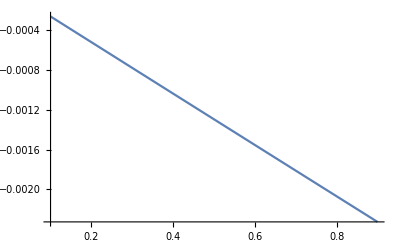

```mathematica
Plot[ Evaluate[ V2[z]-( V2interp[z]) /. intUV[test1][0.1,0.0001,0.8] ],{z, 0.1,0.9} , PlotRange-> All]
```